# Bifurcations in planar, quadratic mass-action networks with few reactions and low molecularity

Murad Banaji^1, Balázs Boros^2, Josef Hofbauer^2

Mathematical Institute, University of Oxford, United Kingdom
 Department of Mathematics, University of Vienna, Austria

This Mathematica Notebook contains the calculations indicated in the paper that has the same title as this file. Running the entire notebook takes about 15 minutes.

## 0 Preliminaries

We have to compute the first focal value in order to figure out whether an Andronov-Hopf bifurcation is supercritical, subcritical, or degenerate. When the first focal value vanishes, we compute the second focal value. When that vanishes, too, we compute the third focal value. For the theoretical background on the computation of the focal values, see Chapter 4 in the book Qualitative Theory of Planar Differential Systems by Dumortier, LLibre, and Artés (which is based on works by Gasull and Torregrosa). By (the proof of) Theorem 8.15 (Kapteyn-Bautin Theorem), in that book, for planar quadratic systems, if the first, second, and third focal values all vanish, the equilibrium is a center (and the Andronov-Hopf bifurcation is vertical).

Below we derive the first, the second, and the third focal value, but only in the quadratic case.

```mathematica
(* F[i,j] computes the polynomial Subscript[F, i](Subscript[h, j]) *)
F[i_,j_] := Module[{coeffs,M,mtx},
coeffs = CoefficientList[D[Subscript[R, i] Subscript[h, j],{z,1}],{z,w}];
M = Dimensions[coeffs][[1]]-1;
mtx = (coeffs + Transpose[coeffs*]) Table[If[k+l==M&&k≠l,1/(k-l),0],{k,0,M},{l,0,M}];
I (z^Range[0,M]).mtx.w^Range[0,M]
];

(* H[k,j] computes Subscript[H, k](Subscript[h, j]), note that one of k and j is even, the other one is odd in all of the interesting cases *)
H[k_,j_] := Module[{coeffs},
coeffs = CoefficientList[Subscript[h, j],{z,w}];
Sum[Coefficient[Subscript[R, k],z^a w^(k-a)]coeffs[[((k-2a+1)+j)/2+1,(j-(k-2a+1))/2+1]],{a,(k+1-j)/2,(k+1+j)/2}]
];

(* compute the focal values Subscript[L, 1],Subscript[L, 2],...,Subscript[L, m] *)
FocalValues[m_,coefficient_,isquadratic_]:=Module[{cd,R2cd,coeffsxy,cond,cd2FG,Ls,quadratic,FG2fg},
(* coefficient is either "Taylor" (Subscript[F, ij] and Subscript[G, ij]) or "derivative" (Subscript[f, ij] and Subscript[g, ij]), where Subscript[F, ij]=Subscript[f, ij]/(i!j!) and Subscript[G, ij]=Subscript[g, ij]/(i!j!); default is Taylor *)
cd = {}; R2cd = {};
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,{cd=Join[cd,{Subscript[c, k,i],Subscript[d, k,i]}], R2cd = Join[R2cd,{Subscript[R, k,i]->Subscript[c, k,i]+Subscript[d, k,i] I}]}]];
coeffsxy = CoefficientList[ComplexExpand[Sum[Sum[Subscript[R, k,i] z^(k-i)(z*)^i,{i,0,k}], {k,2,2m+1}]/.R2cd/.{z->x+y I}], {x,y}];
cond = True;
For[k=2, k≤2m+1, k++,{
 For[i=0, i≤k, i++,{
cond = cond && (Subscript[F, i,k-i]==ComplexExpand[Re[coeffsxy[[i+1,k-i+1]]]]) &&(Subscript[G, i,k-i]==ComplexExpand[Im[coeffsxy[[i+1,k-i+1]]]])
}];
}];
cd2FG = Solve[cond,cd][[1]];
If[isquadratic,{
quadratic={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++,If[i+j>=3,quadratic=Join[quadratic,{Subscript[F, i,j]->0,Subscript[G, i,j]->0}]]]];
cd2FG=cd2FG/.quadratic;
}];

For[k=2, k≤2m+1, k++, Subscript[R, k]=Sum[Subscript[R, k,i] z^(k-i)w^i,{i,0,k}]];

Subscript[h, 0] = 1;
For[k=1, k≤2m-1, k++, Subscript[h, k] = Sum[F[k+1-l,l],{l,0,k-1}]];

Ls=ConstantArray[Null,m];
For[j=1,j≤m,j++,{
Ls[[j]]=Simplify[ComplexExpand[2π Re[Sum[H[2j+1-l,l],{l,0,2j-1}]]/.R2cd/.cd2FG]];
}];
If[coefficient=="derivatives",{
FG2fg={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++,FG2fg=Join[FG2fg,{Subscript[F, i,j]->Subscript[f, i,j]/(i!j!),Subscript[G, i,j]->Subscript[g, i,j]/(i!j!)}]]];
Ls=Simplify[Ls/.FG2fg];
}];
Ls
];

{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3]}=FocalValues[3,"derivatives",True];
Clear[F,H];
```

We display the first focal value, , the second focal value, , and the third focal value, . Important note: here  and  are the partial derivatives (not including the division by ):

```mathematica
Print[" ",Subscript[L, 1]];
Print[" ",Subscript[L, 2]];
Print[" ",Subscript[L, 3]];
```

1/8 π (f_(1,1) f_(2,0)+f_(0,2) (f_(1,1)+g_(0,2))-g_(0,2) g_(1,1)-f_(2,0) g_(2,0)-g_(1,1) g_(2,0))

1/384 π (-24 f_(1,1)^3 f_(2,0)-6 f_(2,0)^3 g_(0,2)+6 f_(2,0) g_(0,2)^3+5 f_(0,2)^3 (f_(1,1)+g_(0,2))+53 f_(2,0)^2 g_(0,2) g_(1,1)+43 g_(0,2)^3 g_(1,1)+86 f_(2,0) g_(0,2) g_(1,1)^2+24 g_(0,2) g_(1,1)^3-f_(0,2)^2 (f_(1,1) (9 f_(2,0)+6 g_(1,1))+g_(1,1) (11 g_(0,2)-5 g_(2,0))+f_(2,0) (14 g_(0,2)-5 g_(2,0)))+43 f_(2,0)^3 g_(2,0)+53 f_(2,0) g_(0,2)^2 g_(2,0)+133 f_(2,0)^2 g_(1,1) g_(2,0)+57 g_(0,2)^2 g_(1,1) g_(2,0)+114 f_(2,0) g_(1,1)^2 g_(2,0)+24 g_(1,1)^3 g_(2,0)+14 f_(2,0) g_(0,2) g_(2,0)^2+9 g_(0,2) g_(1,1) g_(2,0)^2-5 f_(2,0) g_(2,0)^3-5 g_(1,1) g_(2,0)^3+f_(1,1)^2 (32 g_(1,1) (g_(0,2)+g_(2,0))+f_(2,0) (-86 g_(0,2)+6 g_(2,0)))-f_(0,2) (24 f_(1,1)^3+43 g_(0,2)^3+6 g_(0,2) g_(1,1)^2+f_(2,0)^2 (53 g_(0,2)-20 g_(2,0))+6 f_(2,0) g_(1,1) (9 g_(0,2)-7 g_(2,0))+20 g_(0,2)^2 g_(2,0)-22 g_(1,1)^2 g_(2,0)+5 g_(0,2) g_(2,0)^2+2 f_(1,1)^2 (57 g_(0,2)+11 g_(2,0))+f_(1,1) (57 f_(2,0)^2+133 g_(0,2)^2+84 f_(2,0) g_(1,1)+32 g_(1,1)^2+42 g_(0,2) g_(2,0)+5 g_(2,0)^2))+f_(1,1) (-43 f_(2,0)^3-78 f_(2,0)^2 g_(1,1)+6 g_(1,1) (13 g_(0,2)^2+14 g_(0,2) g_(2,0)+g_(2,0)^2)+f_(2,0) (-53 g_(0,2)^2-32 g_(1,1)^2+54 g_(0,2) g_(2,0)+11 g_(2,0)^2)))

1/73728 π (2432 f_(1,1)^5 f_(2,0)+1764 f_(2,0)^5 g_(0,2)-1764 f_(2,0) g_(0,2)^5+135 f_(0,2)^5 (f_(1,1)+g_(0,2))-10644 f_(2,0)^4 g_(0,2) g_(1,1)-29370 f_(2,0)^2 g_(0,2)^3 g_(1,1)-11034 g_(0,2)^5 g_(1,1)-46903 f_(2,0)^3 g_(0,2) g_(1,1)^2-41957 f_(2,0) g_(0,2)^3 g_(1,1)^2-53680 f_(2,0)^2 g_(0,2) g_(1,1)^3-10486 g_(0,2)^3 g_(1,1)^3-21572 f_(2,0) g_(0,2) g_(1,1)^4-2432 g_(0,2) g_(1,1)^5-15 f_(0,2)^4 (f_(1,1) (48 f_(2,0)+31 g_(1,1))+g_(1,1) (40 g_(0,2)-9 g_(2,0))+f_(2,0) (57 g_(0,2)-9 g_(2,0)))-11034 f_(2,0)^5 g_(2,0)-25338 f_(2,0)^3 g_(0,2)^2 g_(2,0)-14676 f_(2,0) g_(0,2)^4 g_(2,0)-54535 f_(2,0)^4 g_(1,1) g_(2,0)-81132 f_(2,0)^2 g_(0,2)^2 g_(1,1) g_(2,0)-18965 g_(0,2)^4 g_(1,1) g_(2,0)-97781 f_(2,0)^3 g_(1,1)^2 g_(2,0)-67875 f_(2,0) g_(0,2)^2 g_(1,1)^2 g_(2,0)-76500 f_(2,0)^2 g_(1,1)^3 g_(2,0)-12190 g_(0,2)^2 g_(1,1)^3 g_(2,0)-24652 f_(2,0) g_(1,1)^4 g_(2,0)-2432 g_(1,1)^5 g_(2,0)-9361 f_(2,0)^3 g_(0,2) g_(2,0)^2-8891 f_(2,0) g_(0,2)^3 g_(2,0)^2-19306 f_(2,0)^2 g_(0,2) g_(1,1) g_(2,0)^2-7662 g_(0,2)^3 g_(1,1) g_(2,0)^2-8463 f_(2,0) g_(0,2) g_(1,1)^2 g_(2,0)^2+822 g_(0,2) g_(1,1)^3 g_(2,0)^2+3651 f_(2,0)^3 g_(2,0)^3+539 f_(2,0) g_(0,2)^2 g_(2,0)^3+11028 f_(2,0)^2 g_(1,1) g_(2,0)^3+1124 g_(0,2)^2 g_(1,1) g_(2,0)^3+9903 f_(2,0) g_(1,1)^2 g_(2,0)^3+2526 g_(1,1)^3 g_(2,0)^3+855 f_(2,0) g_(0,2) g_(2,0)^4+720 g_(0,2) g_(1,1) g_(2,0)^4-135 f_(2,0) g_(2,0)^5-135 g_(1,1) g_(2,0)^5+4 f_(1,1)^4 (-932 g_(1,1) (g_(0,2)+g_(2,0))+f_(2,0) (5393 g_(0,2)+765 g_(2,0)))-f_(0,2)^3 (2526 f_(1,1)^3+3651 g_(0,2)^3-725 g_(0,2) g_(1,1)^2-6 f_(2,0) g_(1,1) (46 g_(0,2)-25 g_(2,0))+893 g_(0,2)^2 g_(2,0)+45 g_(1,1)^2 g_(2,0)+7 f_(2,0)^2 (77 g_(0,2)+15 g_(2,0))+f_(1,1)^2 (9903 g_(0,2)+773 g_(2,0))+2 f_(1,1) (562 f_(2,0)^2+5514 g_(0,2)^2+657 f_(2,0) g_(1,1)+140 g_(1,1)^2+833 g_(0,2) g_(2,0)))+2 f_(1,1)^3 (5243 f_(2,0)^3+11658 f_(2,0)^2 g_(1,1)+4 f_(2,0) (6710 g_(0,2)^2+1466 g_(1,1)^2+520 g_(0,2) g_(2,0)-339 g_(2,0)^2)-2 g_(1,1) (6179 g_(0,2)^2+7312 g_(0,2) g_(2,0)+1133 g_(2,0)^2))+f_(1,1)^2 (6 f_(2,0)^2 g_(1,1) (10175 g_(0,2)-3451 g_(2,0))+f_(2,0)^3 (41957 g_(0,2)+979 g_(2,0))-4 g_(1,1) (g_(0,2)+g_(2,0)) (12493 g_(0,2)^2+2932 g_(1,1)^2+4147 g_(0,2) g_(2,0)-70 g_(2,0)^2)+f_(2,0) (46903 g_(0,2)^3-18159 g_(0,2)^2 g_(2,0)-36184 g_(1,1)^2 g_(2,0)-14467 g_(0,2) g_(2,0)^2-725 g_(2,0)^3))+f_(0,2)^2 (f_(1,1)^3 (-822 f_(2,0)+1020 g_(1,1))+f_(2,0)^3 (8891 g_(0,2)-3373 g_(2,0))+4 f_(2,0)^2 g_(1,1) (5109 g_(0,2)-2506 g_(2,0))+f_(2,0) (9361 g_(0,2)^3+14467 g_(0,2) g_(1,1)^2+4631 g_(0,2)^2 g_(2,0)-9599 g_(1,1)^2 g_(2,0))+f_(1,1)^2 (2 g_(1,1) (7697 g_(0,2)+2007 g_(2,0))+f_(2,0) (8463 g_(0,2)+4649 g_(2,0)))+4 g_(1,1) (2897 g_(0,2)^3+1119 g_(0,2)^2 g_(2,0)-737 g_(1,1)^2 g_(2,0)+3 g_(0,2) (226 g_(1,1)^2-5 g_(2,0)^2))+2 f_(1,1) (3831 f_(2,0)^3+9614 f_(2,0)^2 g_(1,1)+g_(1,1) (13311 g_(0,2)^2+2266 g_(1,1)^2+3885 g_(0,2) g_(2,0))+f_(2,0) (9653 g_(0,2)^2+8154 g_(1,1)^2+4280 g_(0,2) g_(2,0)+30 g_(2,0)^2)))+f_(0,2) (2432 f_(1,1)^5+11034 g_(0,2)^5-979 g_(0,2)^3 g_(1,1)^2-3060 g_(0,2) g_(1,1)^4+f_(2,0)^4 (14676 g_(0,2)-9695 g_(2,0))+10 f_(2,0)^3 g_(1,1) (3398 g_(0,2)-3921 g_(2,0))+9695 g_(0,2)^4 g_(2,0)-13953 g_(0,2)^2 g_(1,1)^2 g_(2,0)-6140 g_(1,1)^4 g_(2,0)+3373 g_(0,2)^3 g_(2,0)^2-4649 g_(0,2) g_(1,1)^2 g_(2,0)^2+105 g_(0,2)^2 g_(2,0)^3+773 g_(1,1)^2 g_(2,0)^3-135 g_(0,2) g_(2,0)^4+4 f_(1,1)^4 (6163 g_(0,2)+1535 g_(2,0))+2 f_(1,1)^3 (6095 f_(2,0)^2+38250 g_(0,2)^2+12168 f_(2,0) g_(1,1)+5864 g_(1,1)^2+16320 g_(0,2) g_(2,0)+1474 g_(2,0)^2)+f_(2,0)^2 (25338 g_(0,2)^3-56015 g_(1,1)^2 g_(2,0)+893 g_(2,0)^3+g_(0,2) (18159 g_(1,1)^2-4631 g_(2,0)^2))-2 f_(2,0) g_(1,1) (-13022 g_(0,2)^3+6331 g_(0,2)^2 g_(2,0)+17 g_(2,0) (960 g_(1,1)^2-49 g_(2,0)^2)+40 g_(0,2) (52 g_(1,1)^2+107 g_(2,0)^2))+f_(1,1)^2 (97781 g_(0,2)^3+56015 g_(0,2)^2 g_(2,0)+45 g_(2,0)^3+4 f_(2,0) g_(1,1) (27005 g_(0,2)+3721 g_(2,0))+3 f_(2,0)^2 (22625 g_(0,2)+4651 g_(2,0))+g_(0,2) (36184 g_(1,1)^2+9599 g_(2,0)^2))+f_(1,1) (18965 f_(2,0)^4+54535 g_(0,2)^4+60050 f_(2,0)^3 g_(1,1)+3728 g_(1,1)^4+39210 g_(0,2)^3 g_(2,0)-4014 g_(1,1)^2 g_(2,0)^2-135 g_(2,0)^4+2 f_(2,0) g_(1,1) (53533 g_(0,2)^2+14624 g_(1,1)^2-3885 g_(2,0)^2)+2 f_(2,0)^2 (40566 g_(0,2)^2+33280 g_(1,1)^2+6331 g_(0,2) g_(2,0)-2238 g_(2,0)^2)+14 g_(0,2)^2 (1479 g_(1,1)^2+716 g_(2,0)^2)-2 g_(0,2) (7442 g_(1,1)^2 g_(2,0)-75 g_(2,0)^3)))+f_(1,1) (11034 f_(2,0)^5+39973 f_(2,0)^4 g_(1,1)+2 f_(2,0)^3 (14685 g_(0,2)^2+24986 g_(1,1)^2-13022 g_(0,2) g_(2,0)-5794 g_(2,0)^2)+2 f_(2,0)^2 (12358 g_(1,1)^3-17 g_(1,1) g_(2,0) (3149 g_(0,2)+783 g_(2,0)))-g_(1,1) (g_(0,2)+g_(2,0)) (39973 g_(0,2)^3+20077 g_(0,2)^2 g_(2,0)+3 g_(0,2) (7772 g_(1,1)^2-283 g_(2,0)^2)+15 g_(2,0) (68 g_(1,1)^2-31 g_(2,0)^2))+2 f_(2,0) (5322 g_(0,2)^4+1864 g_(1,1)^4-16990 g_(0,2)^3 g_(2,0)-7697 g_(1,1)^2 g_(2,0)^2+300 g_(2,0)^4-3 g_(0,2)^2 (10175 g_(1,1)^2+3406 g_(2,0)^2)-2 g_(0,2) (27005 g_(1,1)^2 g_(2,0)+69 g_(2,0)^3))))

We define several modules that are used below.

```mathematica
GetRHS[ntw_]:=Module[{Γ,Γsrc,Γtgt},
{Γ,Γsrc,Γtgt}=GetΓ[ntw];
Γ.(parameters*Apply[Times,variables^Γsrc])
];

CplxStr[cplx_]:=Module[{str,a,coeff,l},
str="";
For[i=1,i<=n,i++,{
a=cplx[[i]];
If[a>=1,{
coeff=If[a>=2,ToString[a],""];
str=StringJoin[str,coeff,species[[i]],"+"];
}];
}];
l=StringLength[str];
If[l==0,str="0",str=StringTake[str,l-1]];
str
];

AddSpace[str_,preorpost_,total_]:=Module[{l,spaces,strnew},
l=StringLength[str];
spaces=StringRepeat[" ",total-l];
If[preorpost=="pre",strnew=StringJoin[spaces,str]];
If[preorpost=="post",strnew=StringJoin[str,spaces]];
strnew
];

NtwToString[ntw_]:=Module[{Γ,Γsrc,Γtgt,str,src,tgt},
{Γ,Γsrc,Γtgt}=GetΓ[ntw];
str="";
For[k=1,k<=Length[ntw],k++,{
src=Γsrcᵀ[[k]];
tgt=Γtgtᵀ[[k]];
str=StringJoin[str,AddSpace[CplxStr[src],"pre",lsrc]," ⟶ ",AddSpace[CplxStr[tgt],"post",ltgt],"  "];
}];
str
];

PrintNtw[ntw_,j_:-1]:=Module[{str},
str=NtwToString[ntw];
If[j!=-1,str=PreNumber[j]<>str];
Print[Style[str,Blue]];
];

PreNumber[j_]:=Module[{},
AddSpace["("<>ToString[j]<>")","pre",6]
];

NtwsBasic[allsrcs_,alltgts_,m_,redundants_:{}]:=Module[{rxns,src,tgt,rxn,},
rxns={};
For[i=1,i<=Length[allsrcs],i++,{
src=allsrcs[[i]];
For[j=1,j<=Length[alltgts],j++,{
tgt=alltgts[[j]];
If[src!=tgt,{
rxn=Join[src,tgt];
If[Not[MemberQ[redundants,rxn]],rxns=Join[rxns,{rxn}]];
}];
}];
}];
Subsets[rxns,{m}]
];

NtwsFilter[ntws_,bifurcation_]:=Module[{list,ntw,Γ,Γsrc,Γtgt,condition},
list={};
Monitor[
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
{Γ,Γsrc,Γtgt}=GetΓ[ntw];
condition=Switch[bifurcation,"fold",CountDistinct[Γsrcᵀ]==4&&MatrixRank[Γ]==2,
"Andronov-Hopf",MemberQ[Γsrcᵀ,{1,1}]&&(MemberQ[ntw,{2,0,3,0}]||MemberQ[ntw,{0,2,0,3}])&&MatrixRank[Differences[Γsrcᵀ]]==2&&MatrixRank[Γ]==2,
"center",MemberQ[Γsrcᵀ,{1,1}]&&MatrixRank[Differences[Γsrcᵀ]]==2&&MatrixRank[Γ]==2];
If[condition,{
If[Resolve[Exists[{α,β},{α,β}.NullSpace[Γ]>0]],{
list=Join[list,{j}];
}];
}];
}],
ProgressIndicator[j,{1,Length[ntws]}]];
ntws[[list]]
];

NtwsNonisomorphic[ntws_]:=Module[{ntwsnew,ntw,ntwswapped},
ntwsnew={};
Monitor[
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
ntwswapped=Sort[ntw[[All,{2,1,4,3}]]];
If[Not[MemberQ[ntwsnew,ntwswapped]],ntwsnew=Join[ntwsnew,{Sort[ntw]}]];
}],
ProgressIndicator[j,{1,Length[ntws]}]];
ntwsnew
];

NtwsNondegEq[ntws_]:=Module[{list,fg,str,J,nondeg},
list={};
Monitor[
For[j=1,j<=Length[ntws],j++,{
fg=GetRHS[ntws[[j]]];
J=D[fg,{variables}];
nondeg=FindInstance[fg==0&&Det[J]!=0&&xypositive&&κpositive,varspars];
If[Length[nondeg]>=1,list=Join[list,{j}]];
}],
ProgressIndicator[j,{1,Length[ntws]}]];
ntws[[list]]
];

NtwsCandidates[ntws_,bifurcation_]:=Module[{list,fg,J,bif,condition},
list={};
Monitor[
For[j=1,j<=Length[ntws],j++,{
fg=GetRHS[ntws[[j]]];
J=D[fg,{variables}];
condition=Switch[bifurcation,"fold",Det[J]==0,"Andronov-Hopf",Tr[J]==0&&Det[J]>0,"Bogdanov-Takens",Tr[J]==0&&Det[J]==0];
bif=FindInstance[fg==0&&condition&&allpositive,varspars];
If[Length[bif]>=1,list=Join[list,{j}]];
}],ProgressIndicator[j,{1,Length[ntws]}]];
ntws[[list]]
];

AnalyseFold[ntws_]:=Module[{onlydoublezero,count,founddegen,foundnontransversal,ntw,fg,J,fold,tracecond,condition,JJ,q,p,B,a,pars,degen,h,Dh,bs,nottransversal,nfold,both,neg,pos,signOtherEigVal},
onlydoublezero={};
count={0,0};
founddegen=False;
foundnontransversal=False;
signOtherEigVal=ConstantArray[False,{2,Length[ntws]}];
Monitor[
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}];
fold=FindInstance[fg==0&&Tr[J]!=0&&Det[J]==0&&allpositive,varspars];
If[Length[fold]>=1,{
tracecond={Tr[J]<0,Tr[J]>0};
For[k=1,k<=Length[tracecond],k++,{
fold=Simplify[Solve[fg==0&&tracecond[[k]]&&Det[J]==0&&allpositive]];
If[Length[fold]>=1,{
signOtherEigVal[[k,j]]=True;
count[[k]]++;
condition=fold[[1,1,2,2]];
fold=Normal[fold[[1]]];
(* nondegeneracy *)
JJ=Simplify[J/.fold];
q=NullSpace[JJ][[1]];
p=NullSpace[JJᵀ][[1]];
B[x_,y_]:=Sum[Simplify[D[fg,{variables[[k]],1},{variables[[l]],1}]/.fold]x[[k]]y[[l]],{k,n},{l,n}];
a=FullSimplify[p.B[q,q],condition];
pars=Complement[varspars,fold[[All,1]]];
degen=FindInstance[a==0&&condition,pars];
If[Length[degen]>=1,founddegen=True];
(* transversality *)
If[Not[IsTransversalNtw[fg,J,"fold"]],foundnontransversal=True];
}];
}];;
},{
onlydoublezero=Join[onlydoublezero,{j}];
}];
}],ProgressIndicator[j,{1,Length[ntws]}]];
Print["Whenever there is a zero and a nonzero eigenvalue, the fold bifurcation is transversal and nondegenerate."];
signOtherEigVal
];

PrintFold[signOtherEigVal_]:=Module[{onlydoublezero,onlynegative,onlypositive,both,nfold},
onlydoublezero=Count[MapThread[And,Map[Not,signOtherEigVal,{2}]],True];
onlynegative=Length[Intersection[Position[signOtherEigVal[[1]],True],Position[signOtherEigVal[[2]],False]]];
onlypositive=Length[Intersection[Position[signOtherEigVal[[1]],False],Position[signOtherEigVal[[2]],True]]];
both=Count[MapThread[And,signOtherEigVal],True];
nfold=Dimensions[signOtherEigVal][[2]]-onlydoublezero;
Print["There are ",onlydoublezero," networks for which the zero eigenvalue always has an algebraic multiplicity of two."];
Print["For the remaining ",nfold," networks, at the critical value, the nonzero eigenvalue\n   * can only be negative in ",onlynegative," networks,\n   * can only be positive in ",onlypositive," networks,\n   * can be positive or negative in ",both," networks."];
];

CommonSrcSet[ntws_]:=Module[{groups,srcss,srcs,found,l,Γ,Γsrc,Γtgt,k1,k2,k},
groups={};
l=Length[groups];
srcss={};
For[j=1,j<=Length[ntws],j++,{
{Γ,Γsrc,Γtgt}=GetΓ[ntws[[j]]];
found=False;
i=1;
While[i<=n!&&Not[found],{
srcs=Sort[Γsrc[[πspecies[[i]]]]ᵀ];
If[MemberQ[srcss,srcs],{
k=FirstPosition[srcss,srcs][[1]];
groups[[k]]=Join[groups[[k]],{j}];
found=True;
},{
i++;
}];
}];
If[Not[found],{
srcss=Join[srcss,{Sort[Γsrcᵀ]}];
l=l+1;
groups=Join[groups,{{j}}];
}];
}];
{srcss,groups}
];

PermutedΓss[srcs_,ntws_]:=Module[{Γss,Γ,Γsrc,Γtgt,Γs,τ,ρ},
Γss=ConstantArray[{},Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
{Γ,Γsrc,Γtgt}=GetΓ[ntws[[j]]];
Γs={};
For[i=1,i<=n!,i++,{
τ=πspecies[[i]];
For[k=1,k<=m!,k++,{
ρ=πreactions[[k]];
If[srcs==Γsrc[[τ,ρ]]ᵀ,Γs=Join[Γs,{Γ[[τ,ρ]]}]];
}];
}];
Γss[[j]]=Γs;
}];
Γss
];

FindDiagEquiv[Γss_,ntws_,srcs_,print_]:=Module[{found,equivj1,Γ1,Γs,j3,noequiv,equiv},
found={};
For[j1=1,j1<=Length[Γss],j1++,{
If[Not[MemberQ[found,j1]],{
equivj1={j1};
Γ1=Γss[[j1]][[1]];
For[j2=j1+1,j2<=Length[Γss],j2++,{
Γs=Γss[[j2]];
j3=1;
noequiv=True;
While[j3<=Length[Γs]&&noequiv,{
equiv=FindInstance[Γ1==Subscript[Δ, 1].Γs[[j3]].Subscript[Δ, 2]&&diagparams>0,diagparams];
If[Length[equiv]>=1,{
noequiv=False;
found=Join[found,{j2}];
equivj1=Join[equivj1,{j2}];
}];
j3++;
}];
}];
If[print=="detailed"&&Length[equivj1]>=2,{
For[j=1,j<=Length[equivj1],j++,{
PrintNtw[ntws[[equivj1[[j]]]]];
}];
Print[StringRepeat["-",55]];
}];
}];
}];
Length[Γss]-Length[found]
];

PrintDiagEquiv[srcss_,dynnonequiv_,diagnonequiv_]:=Module[{},
For[l=1,l<=Length[srcss],l++,{
Print["sources: ",srcss[[l]],"; the ",Style[AddSpace[ToString[dynnonequiv[[l]]],"pre",3],Blue]," dynamically nonequivalent networks fall into ",Style[AddSpace[ToString[diagnonequiv[[l]]],"pre",3],Blue]," diagonally nonequivalent classes"];
}];
Print[StringRepeat[" ",32],"overall, the ",Style[AddSpace[ToString[Total[dynnonequiv]],"pre",3],Blue]," dynamically nonequivalent networks fall into ",Style[AddSpace[ToString[Total[diagnonequiv]],"pre",3],Blue]," diagonally nonequivalent classes"];
];


FindDiagEquivAll[ntwsall_,print_:"no_details"]:=Module[{srcss,groups,srcs,ntws,Γss,dynnonequiv,diagnonequiv},
{srcss,groups}=CommonSrcSet[ntwsall];
dynnonequiv=ConstantArray[Null,Length[groups]];
diagnonequiv=ConstantArray[Null,Length[groups]];
Monitor[
For[l=1,l<=Length[groups],l++,{
srcs=srcss[[l]];
ntws=ntwsall[[groups[[l]]]];
Γss=PermutedΓss[srcs,ntws];
dynnonequiv[[l]]=Length[groups[[l]]];
diagnonequiv[[l]]=FindDiagEquiv[Γss,ntws,srcs,print];
}],ProgressIndicator[l,{1,Length[groups]}]];
PrintDiagEquiv[srcss,dynnonequiv,diagnonequiv];
];

PrintNtwEquil[ntws_,function_]:=Module[{ntw,fg,equil},
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
PrintNtw[ntw,j];
fg=GetRHS[ntw];
If[function=="Reduce",equil=Reduce[fg==0&&allpositive,{x,y}]];
If[function=="Solve",{
equil=Simplify[Solve[fg==0&&allpositive,{Subscript[κ, 4],x}]];
If[Length[equil]==0,equil=Simplify[Solve[fg==0&&allpositive,{Subscript[κ, 4],y}]]];
}];
Print[StringRepeat[" ",8],equil];
}];
];

AnalyseUniqueEquil[ntws_]:=Module[{foundMPE,ntw,fg,twoequil,MPE},
foundMPE=False;
Monitor[
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
twoequil=fg==0&&(fg/.xy2XY)==0&&{x,y}!={X,Y}&&allpositive&&X>0&&Y>0;
MPE=TimeConstrained[FindInstance[twoequil,{x,y,X,Y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}],0.5,{0,0}];
If[Length[MPE]==2,MPE=FindInstance[Reduce[twoequil],{x,y,X,Y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}]];
If[Length[MPE]==1,{PrintNtw[ntw];foundMPE=True}];
}],ProgressIndicator[j,{1,Length[ntws]}]];
If[Not[foundMPE],Print["Each of the ",Length[ntws]," networks has at most one positive equilibrium."]];
];

(* This module became unnecessary. 
AnalyseAtMostTwoEquil[ntws_]:=Module[{ntw,fg,MPE,configurations,found3equils,threeequil,solution},
configurations={Subscript[x, 1]<Subscript[x, 2]<Subscript[x, 3],Subscript[x, 1]<Subscript[x, 2]==Subscript[x, 3]&&Subscript[y, 2]<Subscript[y, 3],Subscript[x, 1]==Subscript[x, 2]<Subscript[x, 3]&&Subscript[y, 1]<Subscript[y, 2],Subscript[x, 1]==Subscript[x, 2]==Subscript[x, 3]&&Subscript[y, 1]<Subscript[y, 2]<Subscript[y, 3]};
found3equils=ConstantArray[False,Length[ntws]];
Monitor[
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
(* For some of the networks with source complexes , , , , the computation below gets stuck. However, we can safely ignore those networks because it is obvious that no planar, quadratic differential equation with monomials ,,,  can admit three distinct positive equilibria. Some other source quadruples could be treated similarly but since those do not seem to cause a computational issue,we do not bother with handling those separately. *)
If[Sort[ntw[[All,{1,2}]]]!={{0,0},{0,2},{1,0},{2,0}},{
fg=GetRHS[ntw];
threeequil=(fg/.{x->Subscript[x, 1],y->Subscript[y, 1]})==0&&(fg/.{x->Subscript[x, 2],y->Subscript[y, 2]})==0&&(fg/.{x->Subscript[x, 3],y->Subscript[y, 3]})==0&&κpositive&&{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, 3],Subscript[y, 3]}>0;
For[k=1,k<=Length[configurations],k++,{
solution=FindInstance[Reduce[threeequil&&configurations[[k]]],{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, 3],Subscript[y, 3],Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}];
If[Length[solution]>=1,found3equils[[j]]=True];
}];
}];
}],ProgressIndicator[j,{1,Length[ntws]}]];
If[Not[AnyTrue[found3equils,#==True&]],Print["No network admits three positive equilibria."]];
];*)

AnalyseJacobianDeterminant[ntws_]:=Module[{ntw,fg,varsparsXY,J,detJ,detnonnegatives,detnonnegative,twoequil,MPE},
varsparsXY=Join[varspars,{X,Y}];
detnonnegatives=ConstantArray[False,Length[ntws]];
Monitor[For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}];
detJ=Det[J];
twoequil=fg==0&&(fg/.xy2XY)==0&&{x,y}!={X,Y}&&allpositive&&X>0&&Y>0;
detnonnegative=Reduce[twoequil&&detJ(detJ/.xy2XY)>=0];
If[Length[detnonnegative]>=1,detnonnegatives[[j]]=True];
}],ProgressIndicator[j,{1,Length[ntws]}]];
If[Not[AnyTrue[detnonnegatives,#==True&]],{
Print["For any pair of positive equilibria, the Jacobian determinant is positive for one, while it is negative for the other."];
}];
];

SelectBimolecular[ntws_]:=Module[{idxs,tgts},
idxs={};
For[j=1,j<=Length[ntws],j++,{
tgts=ntws[[j]][[All,{3,4}]];
If[AllTrue[Total[tgtsᵀ],#<=2&],idxs=Join[idxs,{j}]];
}];
ntws[[idxs]]
];

PrintBimoleculars[ntws_,lemma_]:=Module[{},
Print["Out of the ",Length[ntws]," quadratic, trimolecular networks in ",lemma," above, ",Length[SelectBimolecular[ntws]]," are bimolecular."];
];

CanonicalFoldBimol[ntws_]:=Module[{ntwscanonical,ntw,srcs,i,Xto2X,Yto2X,list},
ntwscanonical=ConstantArray[Null,Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
srcs=ntw[[All,{1,2}]];
If[MemberQ[ntw,{0,1,0,2}]||(MemberQ[ntw,{1,0,0,2}]&&Not[MemberQ[ntw,{0,1,2,0}]]),ntw=ntw[[All,{2,1,4,3}]]];
If[MemberQ[ntw,{1,0,2,0}],{
i=FirstPosition[ntw,{1,0,2,0}][[1]];
ntw[[{1,i}]]=ntw[[{i,1}]];
},{
i=FirstPosition[ntw,{0,1,2,0}][[1]];
ntw[[{1,i}]]=ntw[[{i,1}]];
}];
If[MemberQ[srcs,{1,1}],{
i=FirstPosition[srcs,{1,1}][[1]];
ntw[[{2,i}]]=ntw[[{i,2}]];
}];
If[MemberQ[ntw,{0,0,0,1}],{
i=FirstPosition[ntw,{0,0,0,1}][[1]];
ntw[[{3,i}]]=ntw[[{i,3}]];
}];
If[MemberQ[ntw,{1,0,0,0}],{
i=FirstPosition[ntw,{1,0,0,0}][[1]];
ntw[[{3,i}]]=ntw[[{i,3}]];
},{
If[MemberQ[ntw,{2,0,0,0}]&&MemberQ[ntw,{0,1,2,0}],{
i=FirstPosition[ntw,{2,0,0,0}][[1]];
ntw[[{3,i}]]=ntw[[{i,3}]];
}];
}];
If[MemberQ[ntw,{2,0,0,2}]&&Not[MemberQ[ntw,{0,0,0,1}]&&MemberQ[ntw,{1,1,0,0}]],{
i=FirstPosition[ntw,{2,0,0,2}][[1]];
ntw[[{2,i}]]=ntw[[{i,2}]];
}];
ntwscanonical[[j]]=ntw;
}];
Xto2X={10,11,12,2,6,3,8,9,24,25};
Yto2X={7,15,23,26,27,28,29,30,4,14,21,22,1,5,13,19,20,16,17,18};
list=Join[Xto2X,Yto2X];
ntwscanonical[[list]]
];

AnalyseFoldBimolecular[ntws_]:=Module[{foundnonnegtrace,ntw,fg,J,tracenonneg},
foundnonnegtrace=False;
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}];
tracenonneg=FindInstance[fg==0&&Tr[J]>=0&&Det[J]==0&&allpositive,varspars];
If[Length[tracenonneg]>=1,foundnonnegtrace=True];
}];
If[Not[foundnonnegtrace],Print["The second eigenvalue is negative for all the ",Length[ntws]," bimolecular networks that admit a fold bifurcation."]];
];

AnalyseBoundaryEquilibria[ntws_]:=Module[{ntw,fg,bdequil,bdequilreduce,J},
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
bdequilreduce=Reduce[fg==0&&κpositive&&{x,y}>=0&&x y==0];
bdequil=Simplify[Solve[bdequilreduce,{x,y}]];
If[Length[bdequil]>=1,{
PrintNtw[ntw,j];
bdequil=Normal[bdequil[[1]]];
J=D[fg,{variables}]/.bdequil;
Print["    boundary equilibrium: ",Style[bdequilreduce,Pink],", and the Jacobian matrix there equals ",MatrixForm[J]];
}];
}];
];

PrintNtws[ntws_]:=Module[{},
For[j=1,j<=Length[ntws],j++,PrintNtw[ntws[[j]],j]];
];

CanonicalAndronovHopf[ntws_]:=Module[{ntwscanonical,ntw,i,srcs,XYto0,XYtoY,XYto2Yor3Y,XYtoXor2Xor3X,XYtwice,list},
ntwscanonical=ConstantArray[Null,Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
If[MemberQ[ntw,{0,2,0,3}],ntw=ntw[[All,{2,1,4,3}]]];
i=FirstPosition[ntw,{2,0,3,0}][[1]];
ntw[[{1,i}]]=ntw[[{i,1}]];
srcs=ntw[[All,{1,2}]];
If[Count[srcs,{1,1}]==1,{
i=FirstPosition[srcs,{1,1}][[1]];
ntw[[{2,i}]]=ntw[[{i,2}]];
If[ntw[[2,{3,4}]]=={1,0}||ntw[[2,{3,4}]]=={2,0}||ntw[[2,{3,4}]]=={3,0},{
If[ntw[[4,{1,2}]]=={1,0},ntw[[{3,4}]]=ntw[[{4,3}]]];
}];
If[ntw[[2,{3,4}]]=={0,0}||ntw[[2,{3,4}]]=={0,1},{
If[ntw[[4,{1,2}]]=={2,0}||(ntw[[4,{1,2}]]=={1,0}&&ntw[[3,{1,2}]]!={2,0}),ntw[[{3,4}]]=ntw[[{4,3}]]];
}];
If[ntw[[2,{3,4}]]=={0,2}||ntw[[2,{3,4}]]=={0,3},{
If[(ntw[[4]]=={0,2,0,0}&&ntw[[3]]!={0,1,0,0})||ntw[[4]]=={0,1,0,0},ntw[[{3,4}]]=ntw[[{4,3}]]];
}];
}];
ntwscanonical[[j]]=ntw;
}];
XYto0={138,140,96,142,177,  93,127,129,
           120,     7,30,  71,105,151,184,133,
           121,     8,31,  72,106,152,185,134,
           124,   11,34,  73,107,153,186,135,
           123,   10,33,  74,108,154,187,136,
           122,     9,32,  75,109,155,188,137};
XYtoY={91,95,92,139,141,97,143,178,94,128,130,
           58,99,145,166,170,171,172,173,174,
           76,113,159,192,77,114,160,193,78,115,161,194,79,116,162,195,80,117,163,196};
XYto2Yor3Y={3,4,24,25,16,17,22,23,1,2,59,60,51,52,53,54,49,50,47,48,
                      37,38,41,42,45,46,39,40,43,44,85,90,84,89,83,88,82,87,81,86,61,62,63,64,65,66,69,70,67,68,
                      12,13,35,36,18,19,28,29,125,126,175,176,
                      100,101,146,147,179,180,131,132,168,169};
XYtoXor2Xor3X={55,98,144,167,5,26,14,20,56,6,27,15,21,57};
XYtwice={118,164,197,119,165,198,102,148,181,103,149,182,104,150,183,
                                                                               110,156,189,111,157,190,112,158,191};
list=Join[XYto0,XYtoY,XYto2Yor3Y,XYtoXor2Xor3X,XYtwice];
ntwscanonical[[list]]
];

AnalyseAndronovHopf[ntws_]:=Module[{groupstarts,grouptexts,verticalAHs,ntw,fg,J,vars,hopfset,eq,condition,ωsubst,derivatives,L1,parsremain,superAH,degenAH,subAH,string,L2,superB,degenB,subB,L3,superTH,degenTH,subTH},
groupstarts={1,49,89,161,165,170,175};
grouptexts={"Group 1 (the second reaction is )","Group 2 (the second reaction is )","Group 3 (the second reaction is  or )","Group 4 (the second reaction is )","Group 5 (the second reaction is )","Group 6 (the second reaction is )","Group 7 (the second reaction is  or  or )"};
verticalAHs={};
For[j=1,j<=Length[ntws],j++,{
If[MemberQ[groupstarts,j],{Print[Style[grouptexts[[FirstPosition[groupstarts,j][[1]]]],Bold,18]]}];
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}]/.xy2XY;
vars={};
If[MemberQ[{45,46,47,60,61,62,63},j],vars={X,Y,Subscript[κ, 2]}];
hopfset=Reduce[(fg/.xy2XY)==0&&Tr[J]==0&&Det[J]>0&&XYpositive&&κpositive,vars];
eq=Simplify[Solve[hopfset,Reals][[1]]];
condition=Reduce[eq[[1]][[2]][[2]]];
eq=Normal[eq];
ωsubst={ω->Sqrt[Simplify[Det[J]/.eq,condition]]};
derivatives=Simplify[GetDerivatives[fg,xy2XY,1]/.eq,condition];
L1=Simplify[Subscript[L, 1]/.derivatives/.ωsubst,condition];
parsremain=Complement[{X,Y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]},eq[[All,1]]];
superAH=Length[FindInstance[L1<0&&condition,parsremain]]>=1;
degenAH=Length[FindInstance[L1==0&&condition,parsremain]]>=1;
subAH=Length[FindInstance[L1>0&&condition,parsremain]]>=1;

string={PreNumber[j]<>NtwToString[ntw]};

If[superAH&&Not[degenAH]&&Not[subAH],string=Join[string,{Style["   supercritical A-H",RGBColor[0,0.5,0]]}]];
If[Not[superAH]&&Not[degenAH]&&subAH,string=Join[string,{Style["     subcritical A-H",Orange]}]];
If[degenAH,{
L2=Simplify[Subscript[L, 2]/.derivatives/.ωsubst];
superB=Length[FindInstance[L2<0&&L1==0&&condition,parsremain]]>=1;
degenB=Length[FindInstance[L2==0&&L1==0&&condition,parsremain]]>=1;
subB=Length[FindInstance[L2>0&&L1==0&&condition,parsremain]]>=1;
If[superAH&&subAH&&superB&&Not[degenB]&&Not[subB],string=Join[string,{Style["   supercritical Bautin",Purple]}]];
If[superAH&&subAH&&Not[superB]&&Not[degenB]&&subB,string=Join[string,{Style["     subcritical Bautin",Purple]}]];
If[degenB,{
L3=Simplify[Subscript[L, 3]/.derivatives/.ωsubst];
superTH=Length[FindInstance[L3<0&&L2==0&&L1==0&&condition,parsremain]]>=1;
degenTH=Length[FindInstance[L3==0&&L2==0&&L1==0&&condition,parsremain]]>=1;
subTH=Length[FindInstance[L3>0&&L2==0&&L1==0&&condition,parsremain]]>=1;
If[superAH&&subAH&&Not[superB]&&Not[subB]&&Not[superTH]&&degenTH&&Not[subTH],
string=Join[string,{Style["   supercritical A-H",RGBColor[0,0.5,0]]},{", "},{Style["vertical A-H",Blue]},{", "},{Style["subcritical A-H",Orange]}]];
If[Not[superAH]&&Not[subAH]&&Not[superB]&&Not[subB]&&Not[superTH]&&degenTH&&Not[subTH],
string=Join[string,{Style["        vertical A-H",Blue]}]];
If[degenTH,verticalAHs=Join[verticalAHs,{j}]];
}];
}];
Print[Row[string]];
}];
ntws[[verticalAHs]]
];

PrintL1[ntw_]:=Module[{fg,J,hopfset,eq,condition,ωsubst,derivatives,L1},
fg=GetRHS[ntw];
J=D[fg,{variables}]/.xy2XY;
hopfset=Reduce[(fg/.xy2XY)==0&&Tr[J]==0&&Det[J]>0&&{X,Y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}>0,{X,Y,Subscript[κ, 4]}];
eq=Simplify[Solve[hopfset,Reals][[1]]];
condition=Reduce[eq[[1]][[2]][[2]]];
eq=Normal[eq];
ωsubst={ω->Sqrt[Simplify[Det[J]/.eq,condition]]};
derivatives=Simplify[GetDerivatives[fg,xy2XY,1]/.eq,condition];
L1=Simplify[Subscript[L, 1]/.derivatives/.ωsubst,condition];
Print["The Andronov-Hopf bifurcation set: ",eq,", where ",condition];
Print[" ",ω/.ωsubst];
Print["The first focal value: ",L1];
];

AndronovHopfVertical[ntws_]:=Module[{ntw,fg,J,eq,eqcondition,derivatives,ωsubst,trJ,hopf,hopfcondition,derivativessimp,L1,L2,L3,verticalHopf},
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}]/.xy2XY;
eq=Simplify[Solve[(fg/.xy2XY)==0&&Det[J]>0&&XYpositive&&κpositive,{X,Y}][[1]]];
eqcondition=eq[[1,2,2]];
eq=Normal[eq];
derivatives=Simplify[Simplify[GetDerivatives[fg,{x->X,y->Y},1]/.eq,eqcondition],Simplify[eqcondition,κpositive]];
ωsubst={ω->Simplify[√(Det[J]/.eq),eqcondition]};
trJ=Simplify[Tr[J/.eq],eqcondition];
hopf=Simplify[Solve[trJ==0&&eqcondition][[1]]];
hopfcondition=hopf[[1,2,2]];
hopf=Normal[hopf];
derivativessimp=Simplify[derivatives/.ωsubst/.hopf,hopfcondition];
L1=Simplify[Subscript[L, 1]/.derivativessimp,hopfcondition];
L2=Simplify[Subscript[L, 2]/.derivativessimp,hopfcondition];
L3=Simplify[Subscript[L, 3]/.derivativessimp,hopfcondition];
verticalHopf=FullSimplify[Reduce[(Tr[J]/.eq)==0&&eqcondition]&&Reduce[L1==0&&L2==0&&L3==0&&hopfcondition],κpositive];
Print[Style[PreNumber[j]<>NtwToString[ntw],Blue],verticalHopf];
}];
];

FrankKamenetskySalnikov[bifurcation_]:=Module[{fg,J,hopfset,eq,condition,derivatives,L1,BT0,BT1,BT2,BTcondition,BTparams,istransversal,product,sidecondition,varsparsall},
fg=Subscript[κ, 1] x{1,0}+Subscript[κ, 2] x y{-1,1}+Subscript[κ, 3] y{0,-1}+Subscript[κ, 4] x^2{1,0}+Subscript[κ, 5]{0,1};
J=D[fg,{variables}];
If[bifurcation=="Andronov-Hopf",{
hopfset=Reduce[(fg/.xy2XY)==0&&Tr[J/.xy2XY]==0&&Det[J/.xy2XY]>0&&{X,Y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4],Subscript[κ, 5]}>0];
eq=Simplify[Solve[hopfset]][[1]];
condition=Simplify[Reduce[eq[[1]][[2]][[2]]]];
eq=Normal[eq];
derivatives=Simplify[GetDerivatives[fg,xy2XY,1]/.eq,condition];
L1=Simplify[Subscript[L, 1]/.derivatives,condition];
Print[" ",L1];
}];
If[bifurcation=="Bogdanov-Takens",{
sidecondition=allpositive&&Subscript[κ, 5]>0;
varsparsall=Join[varspars,{Subscript[κ, 5]}];
{BT0,BT1,BT2,BTcondition,BTparams}=ComputeBT[fg,sidecondition,varsparsall];
product=Simplify[BT1*BT2,BTcondition];
istransversal=IsTransversalNtw[fg,J,bifurcation,sidecondition,varsparsall];
Print["(BT.0) Jordan normal form of the Jacobian matrix: ",MatrixForm[JordanDecomposition[BT0][[2]]]];
Print["(BT.1) and (BT.2)  equals ",product];
Print["(BT.3) transversality holds: ",istransversal];
}];
];

IsTransversalNtw[fg_,J_,bifurcation_,sidecondition_:allpositive,varsparsall_:varspars]:=Module[{bifcondition,biffunction,bifset,c,Dh,nottransversal},
bifcondition=Switch[bifurcation,
"fold",Tr[J]!=0&&Det[J]==0,
"Andronov-Hopf",Tr[J]==0&&Det[J]>0,
"Bogdanov-Takens",Tr[J]==0&&Det[J]==0];
biffunction=Switch[bifurcation,
"fold",{Det[J]},
"Andronov-Hopf",{Tr[J]},
"Bogdanov-Takens",{Tr[J],Det[J]}];
bifset=fg==0&&bifcondition&&sidecondition;
c=Length[biffunction];
Dh=D[Join[fg,biffunction],{varsparsall}];
nottransversal=FindInstance[Reduce[Not[MatrixRank[Dh]==n+c&&MatrixRank[Dh[[All,Range[1,n]]]]==n]&&bifset],varsparsall];
If[Length[nottransversal]>=1,False,True]
];

IsTransversalNtws[ntws_,bifurcation_]:=Module[{istransversal,ntw,fg,J},
istransversal=ConstantArray[Null,Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
J=D[fg,{variables}];
istransversal[[j]]=IsTransversalNtw[fg,J,bifurcation];
}];
istransversal
];

Transversality[ntws_,bifurcation_]:=Module[{istransversal},
istransversal=IsTransversalNtws[ntws,bifurcation];
If[AllTrue[istransversal,#==True&],Print["The "<>bifurcation<>" bifurcation is transversal in all ",Length[ntws]," networks."],Print["Transversality fails for some networks."]];
];

ImaginaryEigvals[ntws_]:=Module[{list,fg,J,imaginary,posrealpart,negrealpart},
list={};
Monitor[
For[j=1,j<=Length[ntws],j++,{
fg=GetRHS[ntws[[j]]];
J=D[fg,{variables}];
imaginary=FindInstance[fg==0&&Tr[J]==0&&Det[J]>0&&allpositive,varspars];
If[Length[imaginary]>=1,{
posrealpart=FindInstance[fg==0&&Tr[J]>0&&Det[J]>0&&allpositive,varspars];
negrealpart=FindInstance[fg==0&&Tr[J]<0&&Det[J]>0&&allpositive,varspars];
If[Length[posrealpart]==0||Length[negrealpart]==0,{
list=Join[list,{j}];
}];
}];
}],
ProgressIndicator[j,{1,Length[ntws]}]];
ntws[[list]]
];

CanonicalCenter[ntws_]:=Module[{ntwsnew,ntw,i,list},
ntwsnew=ConstantArray[Null,Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
If[MemberQ[ntw,{0,1,0,2}]&&MemberQ[ntw,{1,0,0,0}],{
ntw=ntw[[All,{2,1,4,3}]];
}];
i=FirstPosition[ntw,{1,0,2,0}][[1]];
ntw[[{1,i}]]=ntw[[{i,1}]];
i=FirstPosition[ntw,{0,1,0,0}][[1]];
ntw[[{4,i}]]=ntw[[{i,4}]];
If[ntw[[3]]=={1,1,1,2},ntw[[{2,3}]]=ntw[[{3,2}]]];
If[ntw[[3]]=={1,1,0,3},ntw[[{2,3}]]=ntw[[{3,2}]]];
If[ntw[[3]]=={1,1,0,2},ntw[[{2,3}]]=ntw[[{3,2}]]];
ntwsnew[[j]]=ntw;
}];
list={1,2,3,4,8,9,5,6,11,12,13,18,17,21,16,20,15,19,14,10,7};
ntwsnew[[list]]
];

CanonicalBogdanovTakens[ntws_]:=Module[{ntw,ntwsnew,order,srcs,reorder},
ntwsnew=ConstantArray[Null,Length[ntws]];
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
If[MemberQ[ntw,{0,2,0,3}],ntw=ntw[[All,{2,1,4,3}]]];
ntwsnew[[j]]=ntw;
}];

order={{2,0},{1,1},{0,2},{0,1},{0,0},{1,0}};
For[j=1,j<=Length[ntwsnew],j++,{
ntw=ntwsnew[[j]];
srcs=ntw[[All,{1,2}]];
ntwsnew[[j]]=ntw[[Flatten[Position[srcs,#]&/@order]]];
}];
reorder={14,15,20,21,18,19,16,17,26,30,27,31,28,32,29,33,23,24,25,1,2,3,4,5,6,7,8,9,10,11,12,13,22};
ntwsnew[[reorder]]
];

ComputeBT[fg_,sidecondition_:allpositive,varsparsall_:varspars]:=Module[{J,BT,BTcondition,BTparams,BT0,BT1,BT2},
J=D[fg,{variables}];
BT=FullSimplify[Solve[fg==0&&Det[J]==0&&Tr[J]==0&&sidecondition][[1]]];
BTcondition=BT[[1,2,2]];
BTparams=Complement[varsparsall,BT[[All,1]]];
BT=Normal[BT];
BT0=Simplify[J/.BT,BTcondition];
{Subscript[q, 0],Subscript[q, 1],Subscript[p, 0],Subscript[p, 1]}=GetEigenvectors[BT0];
B[x_,y_]:=Sum[Simplify[D[fg,{variables[[k]],1},{variables[[l]],1}]/.BT]x[[k]]y[[l]],{k,n},{l,n}];
BT1=Simplify[Subscript[p, 0].B[Subscript[q, 0],Subscript[q, 0]]+Subscript[p, 1].B[Subscript[q, 0],Subscript[q, 1]]];
BT2=1/2 Simplify[Subscript[p, 1].B[Subscript[q, 0],Subscript[q, 0]]];
{BT0,BT1,BT2,BTcondition,BTparams}
];

AnalyseBogdanovTakens[ntws_]:=Module[{ntw,fg,product,BT0holds,BTcondition,BTparams,BT0,BT1,BT2,BTneg,BTzer,BTpos,signs,ntwstring},
BT0holds=True;
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
{BT0,BT1,BT2,BTcondition,BTparams}=ComputeBT[fg];
If[JordanDecomposition[BT0][[2]]!={{0,1},{0,0}},BT0holds=False];
product=Simplify[BT1*BT2,BTcondition];
BTneg=FindInstance[product<0&&BTcondition,BTparams];
BTzer=FindInstance[product==0&&BTcondition,BTparams];
BTpos=FindInstance[product>0&&BTcondition,BTparams];
signs={Length[BTneg],Length[BTzer],Length[BTpos]};
ntwstring=Style[PreNumber[j]<>NtwToString[ntw],Blue];
If[signs=={1,0,0},Print[ntwstring,Style["supercritical B-T",RGBColor[0,0.5,0]]]];
If[signs=={0,1,0},Print[ntwstring,Style["   degenerate B-T",Blue]]];
If[signs=={0,0,1},Print[ntwstring,Style["  subcritical B-T",Orange]]];
}];
If[BT0holds==False,Print["Condition (BT.0) doesn't hold for all networks!"]];
];

BogdanovTakensVerticalAnalyse[ntw_]:=Module[{fg,J,detJ,trJ,fold,equilibria,eq1,eq2},
fg=GetRHS[ntw];
J=D[fg,{variables}];
detJ=Simplify[Det[J]];
trJ=Simplify[Tr[J]];
fold=Reduce[fg==0&&detJ==0&&allpositive,{Subscript[κ, 1],x,y}];
Print["fold bifurcation: ",fold];
equilibria=Reduce[fg==0&&allpositive,variables];
Print["equilibria: ",equilibria];
eq1=Normal[Simplify[Solve[fg==0&&detJ<0&&allpositive,variables][[1]]]];
eq2=Normal[Simplify[Solve[fg==0&&detJ>0&&allpositive,variables][[1]]]];
Print["the trace of the Jacobian matrix at the equilibrium with positive Jacobian determinant: ",Simplify[trJ/.eq2]];
Print["divergence of the vector field (after multiplying by ): ",Simplify[Div[fg/x,variables]]];
];

BogdanovTakensVerticalStreamPlot[fg_,κsubst_,xylim_,H_]:=Module[{b,h,eq1,eq2,ccenter,csaddle,r,levelsbelow,levels,l,colors,limits,levelcurves,strpl,xaxis,yaxis,peq1,peq2,shw},
b=xylim;
h=Solve[H==c,y];
{eq1,eq2}=Simplify[Solve[Grad[H,variables]==0&&allpositive,variables]]/.κsubst;
ccenter=Simplify[H/.eq2/.κsubst];
csaddle=Simplify[H/.eq1/.κsubst];
r=8;
levelsbelow=Table[(r^2-i^2)/r^2 ccenter+i^2/r^2 csaddle,{i,1,r-1}];
levels=Join[levelsbelow,{csaddle}];
l=Length[levelsbelow]+1;
colors[i_]:=Module[{},Piecewise[{{Blue,i<l},{Red,i==l},{RGBColor[0,0.5,0],i>l}}]];
limits[i_]:=Module[{},Piecewise[{{x/.eq1/.κsubst,i<l},{b,i>=l}}]];
levelcurves=Table[Plot[y/.h/.{c->levels[[i]]}/.κsubst,{x,0,limits[i]},PlotRange->{{0,b},{0,b}},PlotStyle->colors[i]],{i,1,Length[levels]}];
strpl=StreamPlot[fg/.κsubst,{x,0,b},{y,0,b},StreamMarkers->"PinDart",Frame->False,StreamColorFunction->None,ImageSize->Large];
xaxis=ListLinePlot[{{0,0},{b,0}},PlotStyle->{Gray,Thick}];
yaxis=ListLinePlot[{{0,0},{0,b}},PlotStyle->{Gray,Thick}];
peq1=ListPlot[{variables/.eq1/.κsubst},PlotStyle->Red];
peq2=ListPlot[{variables/.eq2/.κsubst},PlotStyle->Blue];
Show[strpl,xaxis,yaxis,levelcurves,peq1,peq2]
];

BogdanovTakensVerticalBifDiagr[]:=Module[{rpl1,rpl2,rpl3,xaxis,yaxis,fold,hopf,BT,txt,arrows},
rpl1=RegionPlot[Subscript[κ, 1]>2,{Subscript[κ, 1],0,3},{Subscript[κ, 2],0,3},PlotStyle->{Darker[Red],Opacity[0.2]},BoundaryStyle->None,Frame->False,PlotRange->{{-0.1,3.2},{-0.1,3.2}},ImageSize->Large];
rpl2=RegionPlot[Subscript[κ, 2]<Subscript[κ, 1]<2,{Subscript[κ, 1],0,3},{Subscript[κ, 2],0,3},PlotStyle->{Darker[Magenta],Opacity[0.2]},BoundaryStyle->None,PlotStyle->Red,MaxRecursion->10];
rpl3=RegionPlot[Subscript[κ, 1]<2&&Subscript[κ, 2]>Subscript[κ, 1],{Subscript[κ, 1],0,3},{Subscript[κ, 2],0,3},PlotStyle->{Darker[Green],Opacity[0.2]},BoundaryStyle->None,PlotStyle->Red,MaxRecursion->10];
xaxis=ListLinePlot[{{0,0},{3,0}},PlotStyle->{Gray,Thick}];
yaxis=ListLinePlot[{{0,0},{0,3}},PlotStyle->{Gray,Thick}];
fold=ListLinePlot[{{2,0},{2,3}},PlotStyle->{Orange,Thick}];
hopf=ListLinePlot[{{0,0},{2,2}},PlotStyle->{Blue,Thick}];
BT=ListPlot[{{2,2}},PlotStyle->Black];
txt=Graphics[{
Text[Style[,Bold,14],{3.1,0}],
Text[Style[,Bold,14],{0,3.1}],
Text[Style["degenerate\nBogdanov-Takens\nbifurcation",Black,Bold,14],{1.3,2.7}],
Text[Style["a saddle and a stable\nequilibrium",Darker[Green],Bold,14],{0.7,2.1}],
Text[Style["a saddle and an unstable\nequilibrium",Darker[Magenta],Bold,14],{1.3,0.25}],
Text[Style[Rotate["no positive equilibrium",90Degree],Darker[Red],Bold,14],{2.75,1.5}],
Text[Style[Rotate["fold bifurcation, one positive equilibrium",90Degree],Orange,Bold,14],{2.08,1.5}],
Text[Style[Rotate["homoclinic orbit surrounding a center",45Degree],Darker[Blue],Bold,14],{1-0.06,1+0.06}],
Text[Style[Rotate["vertical Andronov-Hopf bifurcation",45Degree],Darker[Blue],Bold,14],{1+0.06,1-0.06}]
}];
arrows=Graphics[{{Arrowheads[Medium],Black,Arrow[BezierCurve[{{1.55,2.5},{1.75,2.1},{1.95,2.03}}]]}}];
Show[rpl1,rpl2,rpl3,fold,hopf,BT,arrows,xaxis,yaxis,txt]
];

BogdanovTakensThreeSpecies[fg_,zsubst_,sidecondition_,varsparsall_]:=Module[{FG,BT0,BT1,BT2,BTcondition,BTparams,product,istransversal},
FG=fg[[{1,2}]]/.zsubst;
{BT0,BT1,BT2,BTcondition,BTparams}=ComputeBT[FG,sidecondition,varsparsall];
product=FullSimplify[BT1*BT2,BTcondition];
istransversal=IsTransversalNtw[FG,D[FG,{variables}],"Bogdanov-Takens",sidecondition,varsparsall];
Print["(BT.0) Jordan normal form of the Jacobian matrix: ",MatrixForm[JordanDecomposition[BT0][[2]]]];
Print["(BT.1) and (BT.2)  equals ",product];
Print["(BT.3) transversality holds: ",istransversal];
];

PrintNtwsRHS[ntws_]:=Module[{ntw,fg},
For[j=1,j<=Length[ntws],j++,{
ntw=ntws[[j]];
fg=GetRHS[ntw];
Print[Style[PreNumber[j]<>NtwToString[ntw],Blue],"   r.h.s. ",Simplify[fg]];
}];
];

GetΓ[ntw_]:=Module[{n,Γsrc,Γtgt,Γ},
n=Length[ntw[[1]]]/2;
Γsrc=ntw[[All,Range[1,n]]]ᵀ;
Γtgt=ntw[[All,Range[n+1,2n]]]ᵀ;
Γ=Γtgt-Γsrc;
{Γ,Γsrc,Γtgt}
];

GetEigenvectors[A_]:=Module[{q,p,μ,ν},
Subscript[q, 0]=FullSimplify[NullSpace[A][[1]]];
Subscript[q, 1]=FullSimplify[LinearSolve[A,Subscript[q, 0]]];
Subscript[p, 1]=FullSimplify[NullSpace[Aᵀ][[1]]];
Subscript[p, 0]=FullSimplify[LinearSolve[Aᵀ,Subscript[p, 1]]];
μ=√(Subscript[q, 0].Subscript[q, 0]);
Subscript[q, 0]=Simplify[1/μ Subscript[q, 0]];
Subscript[q, 1]=1/μ Subscript[q, 1];
Subscript[q, 1]=Simplify[Subscript[q, 1]-(Subscript[q, 0].Subscript[q, 1])Subscript[q, 0]];
ν=Simplify[Subscript[q, 0].Subscript[p, 0]];
Subscript[p, 1]=Simplify[1/ν Subscript[p, 1]];
Subscript[p, 0]=Subscript[p, 0]-(Subscript[p, 0].Subscript[q, 1])Subscript[p, 1];
Subscript[p, 0]=Simplify[1/ν Subscript[p, 0]];
{Subscript[q, 0],Subscript[q, 1],Subscript[p, 0],Subscript[p, 1]}
];

GetDerivatives[fg_,equilibrium_,m_]:=Module[{J,xyshift,T,Tinvuv,FG,derivatives,a,b,u,v,i,j},
J=Simplify[D[fg,{{x,y}}]/.equilibrium];
xyshift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
T = {{1,0},{-a/ω,-b/ω}};
Tinvuv = Inverse[T].{u,v};
FG = (T . fg/.xyshift)/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{a->J[[1,1]],b-> J[[1,2]]};
derivatives={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, 
derivatives = Join[derivatives, {Subscript[f, i,j]->(D[FG[[1]],{u,i},{v,j}]/.{u->0,v->0}), Subscript[g, i,j]->(D[FG[[2]],{u,i},{v,j}]/.{u->0,v->0})}]]];
derivatives];

srcstrs={"  0","  X","  Y"," 2X","X+Y"," 2Y"};
tgtstrs={"0   ","X   ","Y   ","2X  ","X+Y ","2Y  ","3X  ","2X+Y","X+2Y","3Y  "};
bimol={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}};
trimol={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}};
redundants={{0,0,2,0},{0,0,3,0},{0,0,0,2},{0,0,0,3},{1,0,3,0},{1,0,1,2},{0,1,0,3},{0,1,2,1},{2,0,1,0},{2,0,1,1},{0,2,0,1},{0,2,1,1}};

xy2XY={x->X,y->Y};
XYpositive=X>0&&Y>0;
variables={x,y};
species={"X","Y"};
parameters={Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]};
varspars=Join[variables,parameters];
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
xypositive=variables>0;
allpositive=xypositive&&κpositive;
n=Length[variables];
m=Length[parameters];
lsrc=4;
ltgt=4;
πspecies=Permutations[Range[1,n]];
πreactions=Permutations[Range[1,m]];
Subscript[Δ, 1]=DiagonalMatrix[{Subscript[δ, 1],Subscript[δ, 2]}];
Subscript[Δ, 2]=DiagonalMatrix[{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],Subscript[v, 4]}];
diagparams={Subscript[δ, 1],Subscript[δ, 2],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],Subscript[v, 4]};
```

## 3 Fold bifurcation

### 3.2 Planar networks

#### Lemma 20

We start by generating all two-species, four-reaction, quadratic, trimolecular reaction networks. However, since we are interested only in dynamically nonequivalent networks with four distinct sources, for each source complex we keep only one reaction in each direction (e.g.  and  are allowed, but , , ,  are not). There are 111930 such networks.

```mathematica
ntws0=NtwsBasic[bimol,trimol,m,redundants];
Print["We start with ",Length[ntws0]," networks."];
```

We start with 111930 networks.

Next, we eliminate those networks that have fewer than four distinct source complexes or have rank smaller than two. Furthermore, we keep only the dynamically nontrivial ones. Out of the 111930 networks, 11767 remains.

```mathematica
ntws1=NtwsFilter[ntws0,"fold"];
Print["There remains ",Length[ntws1]," networks. (These have four distinct source complexes, have rank two, and are dynamically nontrivial.)"];
```

There remains 11767 networks. (These have four distinct source complexes, have rank two, and are dynamically nontrivial.)

We keep only one member of each isomorphism class. Practically, we remove one of those networks that differ only in swapping  and . There remains 5897 networks.

```mathematica
ntws2=NtwsNonisomorphic[ntws1];
Print["There remains ",Length[ntws2]," networks. (These are nonisomorphic.)"];
```

There remains 5897 networks. (These are nonisomorphic.)

We filter out those networks that have no positive nondegenerate equilibrium. There remains 5864 networks.

```mathematica
ntws3=NtwsNondegEq[ntws2];
Print["There remains ",Length[ntws3]," networks. (These admit a positive nondegenerate equilibrium.)"];
```

There remains 5864 networks. (These admit a positive nondegenerate equilibrium.)

#### Theorem 21

We check which networks admit a positive equilibrium with a zero eigenvalue. There are 834 such networks.

```mathematica
ntws4=NtwsCandidates[ntws3,"fold"];
Print["In total, ",Length[ntws4]," networks also admit a positive equilibrium with a zero eigenvalue."];
```

In total, 834 networks also admit a positive equilibrium with a zero eigenvalue.

Next, we analyse the 834 networks. We check whether they admit a transversal and nondegenerate fold bifurcation.

```mathematica
signOtherEigVal=AnalyseFold[ntws4];
PrintFold[signOtherEigVal];
```

Whenever there is a zero and a nonzero eigenvalue, the fold bifurcation is transversal and nondegenerate.

There are 3 networks for which the zero eigenvalue always has an algebraic multiplicity of two.

For the remaining 831 networks, at the critical value, the nonzero eigenvalue
   * can only be negative in 792 networks,
   * can only be positive in 6 networks,
   * can be positive or negative in 33 networks.

#### Remark 22 (a)

We search for diagonal equivalence among the 831 networks in Theorem 21.

```mathematica
ntws5=ntws4[[Flatten[Position[MapThread[Or,signOtherEigVal],True]]]];
FindDiagEquivAll[ntws5];
```

sources: {{0,0},{0,1},{1,0},{2,0}}; the  87 dynamically nonequivalent networks fall into  63 diagonally nonequivalent classes

sources: {{0,0},{1,0},{1,1},{2,0}}; the  79 dynamically nonequivalent networks fall into  62 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,0},{2,0}}; the 101 dynamically nonequivalent networks fall into  70 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,0},{1,1}}; the 129 dynamically nonequivalent networks fall into 101 diagonally nonequivalent classes

sources: {{0,0},{0,1},{1,0},{1,1}}; the  41 dynamically nonequivalent networks fall into  34 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,1},{2,0}}; the  31 dynamically nonequivalent networks fall into  22 diagonally nonequivalent classes

sources: {{0,1},{0,2},{1,0},{2,0}}; the  77 dynamically nonequivalent networks fall into  57 diagonally nonequivalent classes

sources: {{0,1},{1,0},{1,1},{2,0}}; the 166 dynamically nonequivalent networks fall into 138 diagonally nonequivalent classes

sources: {{0,2},{1,0},{1,1},{2,0}}; the 120 dynamically nonequivalent networks fall into  92 diagonally nonequivalent classes

overall, the 831 dynamically nonequivalent networks fall into 639 diagonally nonequivalent classes

#### Remark 22 (d)

The three networks for which the zero eigenvalue cannot have an algebraic multiplicity of one.

```mathematica
ntws6=ntws4[[Flatten[Position[MapThread[Or,signOtherEigVal],False]]]];
PrintNtwEquil[ntws6,"Reduce"];
```

(1)  2Y ⟶ 3Y       X ⟶ 0      X+Y ⟶ 2X      2X ⟶ 2X+Y

κ_1>0&&κ_3>0&&((0<κ_4<κ_3^2/(4 κ_1)&&κ_2>0&&(x==κ_2/(2 κ_4)-1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))||x==κ_2/(2 κ_4)+1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))||(κ_4==κ_3^2/(4 κ_1)&&κ_2>0&&x==κ_2/(2 κ_4)-1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))&&y==κ_2/κ_3

(2)  2Y ⟶ 3Y       X ⟶ 0      X+Y ⟶ 3X      2X ⟶ 2X+Y

κ_1>0&&κ_3>0&&((0<κ_4<κ_3^2/(4 κ_1)&&κ_2>0&&(x==κ_2/(4 κ_4)-1/4 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))||x==κ_2/(4 κ_4)+1/4 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))||(κ_4==κ_3^2/(4 κ_1)&&κ_2>0&&x==κ_2/(4 κ_4)-1/4 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))&&y==κ_2/(2 κ_3)

(3)  2Y ⟶ 3Y       X ⟶ 2X     X+Y ⟶ 0       2X ⟶ 2X+Y

κ_1>0&&κ_3>0&&((0<κ_4<κ_3^2/(4 κ_1)&&κ_2>0&&(x==κ_2/(2 κ_4)-1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))||x==κ_2/(2 κ_4)+1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))||(κ_4==κ_3^2/(4 κ_1)&&κ_2>0&&x==κ_2/(2 κ_4)-1/2 √((κ_2^2 κ_3^2-4 κ_1 κ_2^2 κ_4)/(κ_3^2 κ_4^2))))&&y==κ_2/κ_3

#### Remark 22 (f)

The 5864-834=5030 networks that do not admit a fold bifurcation can have only a unique positive equilibrium.

```mathematica
ntws7=Complement[ntws3,ntws4];
AnalyseUniqueEquil[ntws7];
```

Each of the 5030 networks has at most one positive equilibrium.

#### Remark 22 (g)

For any pair of positive equilibria, the Jacobian determinant is positive for one, while it is negative for the other. Hence, three positive equilibria are forbidden. Further, whenever there are two positive equilibria, both are nondegenerate.

```mathematica
AnalyseJacobianDeterminant[ntws4];
```

For any pair of positive equilibria, the Jacobian determinant is positive for one, while it is negative for the other.

#### Remark 22 (h)

We study the 5897-5864=33 networks that admit a positive equilibrium but not a nondegenerate positive equilibrium. We find that there is no positive equilibrium for almost all rate constants, while there is a line of equilibria for an exceptional set of rate constants. That line is either through the origin or vertical or horizontal.

```mathematica
ntws8=Complement[ntws2,ntws3];
PrintNtwEquil[ntws8,"Solve"];
```

(1)   0 ⟶ X        Y ⟶ 0        X ⟶ 0      X+Y ⟶ X+2Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(2)   0 ⟶ X        Y ⟶ 0      X+Y ⟶ X+2Y    2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_1 κ_3^2)/(2 κ_2^2), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_2/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(3)   0 ⟶ X        Y ⟶ 2Y       X ⟶ 0      X+Y ⟶ X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(4)   0 ⟶ X        Y ⟶ 2Y     X+Y ⟶ X       2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_1 κ_3^2)/(2 κ_2^2), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_2/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(5)   0 ⟶ X        Y ⟶ X        X ⟶ 0      X+Y ⟶ 2Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(6)   0 ⟶ X        Y ⟶ X      X+Y ⟶ 2Y      2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_1 κ_3^2)/(2 κ_2^2), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_2/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(7)   0 ⟶ X        Y ⟶ X+2Y     X ⟶ 0      X+Y ⟶ 0

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(8)   0 ⟶ X        Y ⟶ X+2Y   X+Y ⟶ 0       2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_1 κ_3^2)/(2 κ_2^2), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_2/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(9)   Y ⟶ 0        X ⟶ 0      X+Y ⟶ X+2Y    2X ⟶ 3X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(10)   Y ⟶ 2Y      2Y ⟶ 0        X ⟶ 0      X+Y ⟶ 2X+Y

{{κ_4→ConditionalExpression[(2 κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&x>0],y→ConditionalExpression[κ_1/(2 κ_2), κ_1>0&&κ_2>0&&κ_3>0&&x>0]}}

(11)   Y ⟶ 2Y      2Y ⟶ 0        X ⟶ Y      X+Y ⟶ 2X

{{κ_4→ConditionalExpression[(2 κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&x>0],y→ConditionalExpression[κ_1/(2 κ_2), κ_1>0&&κ_2>0&&κ_3>0&&x>0]}}

(12)   Y ⟶ 2Y       X ⟶ 0      X+Y ⟶ X       2X ⟶ 3X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(13)   Y ⟶ 2Y       X ⟶ 2X     X+Y ⟶ X       2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_2 κ_3)/(2 κ_1), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(14)   Y ⟶ X       2Y ⟶ X+2Y     X ⟶ Y       2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_2 κ_3^2)/(2 κ_1^2), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(15)   Y ⟶ X       2Y ⟶ 2X+Y     X ⟶ Y       2X ⟶ Y

{{κ_4→ConditionalExpression[(κ_2 κ_3^2)/κ_1^2, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(16)   Y ⟶ X        X ⟶ 0      X+Y ⟶ 2Y      2X ⟶ 3X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(17)   Y ⟶ X        X ⟶ Y      X+Y ⟶ Y       2X ⟶ 3X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(18)   Y ⟶ X        X ⟶ Y      X+Y ⟶ X       2X ⟶ 2X+Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(19)   Y ⟶ X        X ⟶ Y      X+Y ⟶ 2X+Y    2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_2 κ_3)/(2 κ_1), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(20)   Y ⟶ X        X ⟶ Y      X+Y ⟶ 3X      2X ⟶ Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(21)   Y ⟶ X+Y     2Y ⟶ 0        X ⟶ 0      X+Y ⟶ X+2Y

{{κ_4→ConditionalExpression[(2 κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(22)   Y ⟶ X+Y     2Y ⟶ 0        X ⟶ 0       2X ⟶ 2X+Y

{{κ_4→ConditionalExpression[(2 κ_2 κ_3^2)/κ_1^2, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(23)   Y ⟶ X+Y     2Y ⟶ 3Y       X ⟶ 0      X+Y ⟶ X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(24)   Y ⟶ X+Y     2Y ⟶ X        X ⟶ 0      X+Y ⟶ 3Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(25)   Y ⟶ X+Y     2Y ⟶ X        X ⟶ 0       2X ⟶ X+2Y

{{κ_4→ConditionalExpression[(κ_2 κ_3^2)/κ_1^2, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(26)   Y ⟶ X+Y     2Y ⟶ 2X       X ⟶ 0      X+Y ⟶ 2Y

{{κ_4→ConditionalExpression[(2 κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(27)   Y ⟶ X+Y     2Y ⟶ 2X       X ⟶ 0       2X ⟶ 2Y

{{κ_4→ConditionalExpression[(κ_2 κ_3^2)/κ_1^2, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(28)   Y ⟶ X+Y     2Y ⟶ 2X+Y     X ⟶ 0       2X ⟶ Y

{{κ_4→ConditionalExpression[(κ_2 κ_3^2)/κ_1^2, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(29)   Y ⟶ X+Y      X ⟶ 0      X+Y ⟶ X       2X ⟶ 2X+Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(30)   Y ⟶ X+Y      X ⟶ 0      X+Y ⟶ 2X      2X ⟶ 2Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/(2 κ_1), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(31)   Y ⟶ X+Y      X ⟶ 0      X+Y ⟶ 3X      2X ⟶ Y

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[(y κ_1)/κ_2, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(32)   Y ⟶ X+2Y     X ⟶ 0      X+Y ⟶ 0       2X ⟶ 3X

{{κ_4→ConditionalExpression[(κ_2 κ_3)/κ_1, κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

(33)   Y ⟶ X+2Y     X ⟶ 2X     X+Y ⟶ 0       2X ⟶ 0

{{κ_4→ConditionalExpression[(κ_2 κ_3)/(2 κ_1), κ_1>0&&κ_2>0&&κ_3>0&&y>0],x→ConditionalExpression[κ_1/κ_3, κ_1>0&&κ_2>0&&κ_3>0&&y>0]}}

#### Lemma 23

We count the networks in Lemma 20 that are bimolecular.

```mathematica
PrintBimoleculars[ntws2,"Lemma 20"];
PrintBimoleculars[ntws3,"Lemma 20"];
```

Out of the 5897 quadratic, trimolecular networks in Lemma 20 above, 838 are bimolecular.

Out of the 5864 quadratic, trimolecular networks in Lemma 20 above, 829 are bimolecular.

#### Theorem 24

We count the networks in Theorem 21 that are bimolecular.

```mathematica
PrintBimoleculars[ntws4,"Theorem 21"];
ntwsbimol=SelectBimolecular[ntws4];
ntwsbimol=CanonicalFoldBimol[ntwsbimol];
AnalyseFoldBimolecular[ntwsbimol];
```

Out of the 834 quadratic, trimolecular networks in Theorem 21 above, 30 are bimolecular.

The second eigenvalue is negative for all the 30 bimolecular networks that admit a fold bifurcation.

Next, we print all the 30 bimolecular networks that admit a fold bifurcation.

```mathematica
PrintNtws[ntwsbimol];
```

(1)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y       2X ⟶ 0

(2)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y       2X ⟶ Y

(3)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y       2X ⟶ 2Y

(4)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y        Y ⟶ X

(5)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y        Y ⟶ 2X

(6)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y        Y ⟶ X+Y

(7)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y       2Y ⟶ X

(8)   X ⟶ 2X     X+Y ⟶ 0        0 ⟶ Y       2Y ⟶ 2X

(9)   X ⟶ 2X     X+Y ⟶ 0        Y ⟶ 2Y      2Y ⟶ X

(10)   X ⟶ 2X     X+Y ⟶ 0        Y ⟶ 2Y      2Y ⟶ 2X

(11)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        0 ⟶ Y

(12)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        0 ⟶ X+Y

(13)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ Y

(14)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ X+Y

(15)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ 2Y

(16)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ 0

(17)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ X

(18)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ 2X

(19)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0        0 ⟶ Y

(20)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0        0 ⟶ X+Y

(21)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0       2Y ⟶ 0

(22)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0       2Y ⟶ X

(23)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0        0 ⟶ X

(24)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0        0 ⟶ Y

(25)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0        0 ⟶ X+Y

(26)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0       2Y ⟶ 0

(27)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0       2Y ⟶ X

(28)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ 0

(29)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ X

(30)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ Y

#### Remark 25 (a)

The 30 bimolecular networks that admit a fold bifurcation are diagonally nonequivalent.

```mathematica
FindDiagEquivAll[ntwsbimol];
```

sources: {{0,0},{1,0},{1,1},{2,0}}; the   3 dynamically nonequivalent networks fall into   3 diagonally nonequivalent classes

sources: {{0,0},{0,1},{1,0},{1,1}}; the   5 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,0},{1,1}}; the   4 dynamically nonequivalent networks fall into   4 diagonally nonequivalent classes

sources: {{0,1},{0,2},{1,0},{1,1}}; the  10 dynamically nonequivalent networks fall into  10 diagonally nonequivalent classes

sources: {{0,1},{0,2},{1,1},{2,0}}; the   3 dynamically nonequivalent networks fall into   3 diagonally nonequivalent classes

sources: {{0,0},{0,1},{1,0},{2,0}}; the   3 dynamically nonequivalent networks fall into   3 diagonally nonequivalent classes

sources: {{0,1},{0,2},{1,0},{2,0}}; the   2 dynamically nonequivalent networks fall into   2 diagonally nonequivalent classes

overall, the  30 dynamically nonequivalent networks fall into  30 diagonally nonequivalent classes

#### Lemma 26

We analyse the boundary equilibria of the 30 bimolecular networks that admit a fold bifurcation.

```mathematica
AnalyseBoundaryEquilibria[ntwsbimol];
```

(9)   X ⟶ 2X     X+Y ⟶ 0        Y ⟶ 2Y      2Y ⟶ X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (κ_1 | 0
0 | κ_3)

(10)   X ⟶ 2X     X+Y ⟶ 0        Y ⟶ 2Y      2Y ⟶ 2X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (κ_1 | 0
0 | κ_3)

(13)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ Y

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (-κ_4 | 2 κ_1
κ_4 | -κ_1)

(14)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ X+Y

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (0 | 2 κ_1
κ_4 | -κ_1)

(15)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0        X ⟶ 2Y

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (-κ_4 | 2 κ_1
2 κ_4 | -κ_1)

(16)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ 0

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (0 | 2 κ_1
0 | -κ_1)

(17)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (0 | 2 κ_1
0 | -κ_1)

(18)   Y ⟶ 2X     X+Y ⟶ 2Y      2X ⟶ 0       2Y ⟶ 2X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (0 | 2 κ_1
0 | -κ_1)

(21)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0       2Y ⟶ 0

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(22)   Y ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0       2Y ⟶ X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&y==0&&x==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(26)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0       2Y ⟶ 0

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(27)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0       2Y ⟶ X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(28)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ 0

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(29)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ X

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

(30)   Y ⟶ 2X      2X ⟶ 2Y       X ⟶ 0      X+Y ⟶ Y

boundary equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==0&&y==0, and the Jacobian matrix there equals (-κ_3 | 2 κ_1
0 | -κ_1)

## 4 Andronov-Hopf bifurcation

#### Lemma 28

We determine the base set for Andronov-Hopf bifurcation.

```mathematica
ntws0=NtwsBasic[bimol,trimol,m,redundants];
Print["We start with ",Length[ntws0]," networks."];
```

We start with 111930 networks.

```mathematica
ntws1=NtwsFilter[ntws0,"Andronov-Hopf"];
Print["There remains ",Length[ntws1]," networks. (These are dynamically nontrivial, rank-two networks, whose source complexes do not lie on a line, have a reaction with source , and have  or .)"];
```

There remains 2067 networks. (These are dynamically nontrivial, rank-two networks, whose source complexes do not lie on a line, have a reaction with source , and have  or .)

```mathematica
ntws2=NtwsNonisomorphic[ntws1];
Print["There remains ",Length[ntws2]," networks. (These are nonisomorphic.)"];
```

There remains 1034 networks. (These are nonisomorphic.)

```mathematica
ntws3=NtwsNondegEq[ntws2];
Print["There remains ",Length[ntws3]," networks. (These admit a nondegenerate positive equilibrium.)"];
```

There remains 946 networks. (These admit a nondegenerate positive equilibrium.)

#### Lemma 29

```mathematica
ntws4=NtwsCandidates[ntws3,"Andronov-Hopf"];
Print["In total, ",Length[ntws4]," networks have a positive equilibrium with a pair of purely imaginary eigenvalues."];
```

In total, 198 networks have a positive equilibrium with a pair of purely imaginary eigenvalues.

#### Theorem 30

Next, we bring the 198 networks to “canonical form” and order them. Then we compute and analyse the focal values. Thereby classify the networks according to the type of Andronov-Hopf bifurcation they admit. Further, we verify the transversality of the Andronov-Hopf bifurcation for all the 198 networks.

```mathematica
ntws5=CanonicalAndronovHopf[ntws4];
ntwsVerticalAH=AnalyseAndronovHopf[ntws5];
Transversality[ntws5,"Andronov-Hopf"];
```

Group 1 (the second reaction is )

(1)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ 2Y       Y ⟶ 2X         subcritical A-H

(2)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ 2Y       Y ⟶ 3X         subcritical A-H

(3)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ 3Y       Y ⟶ X          subcritical A-H

(4)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ 3Y       Y ⟶ 2X         subcritical A-H

(5)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ 3Y       Y ⟶ 3X         subcritical A-H

(6)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ X+Y      Y ⟶ X          subcritical A-H

(7)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ X+Y      Y ⟶ 2X         subcritical A-H

(8)  2X ⟶ 3X     X+Y ⟶ 0        X ⟶ X+Y      Y ⟶ 3X         subcritical A-H

(9)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        X ⟶ 2X            vertical A-H

(10)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        0 ⟶ X        supercritical A-H

(11)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        0 ⟶ 2X+Y     supercritical A-H

(12)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        Y ⟶ 0        supercritical A-H

(13)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        Y ⟶ X        supercritical A-H

(14)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        Y ⟶ 2X       supercritical A-H

(15)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        Y ⟶ 3X       supercritical A-H

(16)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        Y ⟶ X+Y      supercritical A-H

(17)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       X ⟶ 2X            vertical A-H

(18)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       0 ⟶ X        supercritical A-H

(19)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       0 ⟶ 2X+Y     supercritical A-H

(20)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       Y ⟶ 0        supercritical A-H

(21)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       Y ⟶ X        supercritical A-H

(22)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       Y ⟶ 2X       supercritical A-H

(23)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       Y ⟶ 3X       supercritical A-H

(24)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       Y ⟶ X+Y      supercritical A-H

(25)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       X ⟶ 2X            vertical A-H

(26)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       0 ⟶ X        supercritical A-H

(27)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       0 ⟶ 2X+Y     supercritical A-H

(28)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       Y ⟶ 0        supercritical A-H

(29)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       Y ⟶ X        supercritical A-H

(30)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       Y ⟶ 2X       supercritical A-H

(31)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       Y ⟶ 3X       supercritical A-H

(32)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       Y ⟶ X+Y      supercritical A-H

(33)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     X ⟶ 2X            vertical A-H

(34)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     0 ⟶ X        supercritical A-H

(35)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     0 ⟶ 2X+Y     supercritical A-H

(36)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     Y ⟶ 0        supercritical A-H

(37)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     Y ⟶ X        supercritical A-H

(38)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     Y ⟶ 2X       supercritical A-H

(39)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     Y ⟶ 3X       supercritical A-H

(40)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     Y ⟶ X+Y      supercritical A-H

(41)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     X ⟶ 2X            vertical A-H

(42)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     0 ⟶ X        supercritical A-H

(43)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     0 ⟶ 2X+Y     supercritical A-H

(44)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     Y ⟶ 0        supercritical A-H

(45)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     Y ⟶ X        supercritical A-H

(46)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     Y ⟶ 2X       supercritical A-H

(47)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     Y ⟶ 3X       supercritical A-H

(48)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     Y ⟶ X+Y      supercritical A-H

Group 2 (the second reaction is )

(49)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ Y        Y ⟶ 2X         subcritical A-H

(50)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ Y        Y ⟶ 3X         subcritical A-H

(51)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2Y       Y ⟶ X          subcritical A-H

(52)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2Y       Y ⟶ 2X         subcritical A-H

(53)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2Y       Y ⟶ 3X         subcritical A-H

(54)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 3Y       Y ⟶ X          subcritical A-H

(55)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 3Y       Y ⟶ 2X         subcritical A-H

(56)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 3Y       Y ⟶ 3X         subcritical A-H

(57)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ X          subcritical A-H

(58)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ 2X         subcritical A-H

(59)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ 3X         subcritical A-H

(60)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 0             vertical A-H

(61)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ X        supercritical A-H, vertical A-H, subcritical A-H

(62)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 2X       supercritical A-H, vertical A-H, subcritical A-H

(63)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 3X       supercritical A-H, vertical A-H, subcritical A-H

(64)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y    2Y ⟶ 0          subcritical A-H

(65)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y    2Y ⟶ X          subcritical A-H

(66)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y    2Y ⟶ 2X         subcritical A-H

(67)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y    2Y ⟶ 3X         subcritical A-H

(68)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y    2Y ⟶ 2X+Y       subcritical A-H

(69)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 0        supercritical A-H

(70)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ X        supercritical A-H

(71)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 2X       supercritical A-H

(72)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 3X       supercritical A-H

(73)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 0        supercritical A-H

(74)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ X        supercritical A-H

(75)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 2X       supercritical A-H

(76)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 3X       supercritical A-H

(77)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ 0        supercritical A-H

(78)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ X        supercritical A-H

(79)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ 2X       supercritical A-H

(80)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ 3X       supercritical A-H

(81)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ 0        supercritical A-H

(82)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ X        supercritical A-H

(83)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ 2X       supercritical A-H

(84)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ 3X       supercritical A-H

(85)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ 0        supercritical A-H

(86)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ X        supercritical A-H

(87)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ 2X       supercritical A-H

(88)  2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ 3X       supercritical A-H

Group 3 (the second reaction is  or )

(89)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ X        supercritical A-H

(90)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X        supercritical A-H

(91)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ 2X+Y     supercritical A-H

(92)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ 2X+Y     supercritical A-H

(93)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ X+Y      supercritical A-H

(94)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X+Y      supercritical A-H

(95)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ X+2Y     supercritical A-H

(96)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X+2Y     supercritical A-H

(97)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ Y        supercritical A-H

(98)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ Y        supercritical A-H

(99)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ 2X+Y     supercritical A-H

(100)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 2X+Y     supercritical A-H

(101)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ X+Y      supercritical A-H

(102)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ X+Y      supercritical A-H

(103)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ 3Y       supercritical A-H

(104)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 3Y       supercritical A-H

(105)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ 2Y       supercritical A-H

(106)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 2Y       supercritical A-H

(107)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ Y        supercritical A-H

(108)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ Y        supercritical A-H

(109)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ X        supercritical A-H

(110)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ X        supercritical A-H

(111)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ 2X       supercritical A-H

(112)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ 2X       supercritical A-H

(113)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ 3X       supercritical A-H

(114)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ 3X       supercritical A-H

(115)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ X+Y      supercritical A-H

(116)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ X+Y      supercritical A-H

(117)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ X+2Y     supercritical A-H

(118)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ X+2Y     supercritical A-H

(119)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ 2X+Y     supercritical A-H

(120)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ 2X+Y     supercritical A-H

(121)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ X+2Y     supercritical A-H

(122)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ X+2Y     supercritical A-H

(123)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ 3Y       supercritical A-H

(124)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ 3Y       supercritical A-H

(125)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ 2Y       supercritical A-H

(126)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ 2Y       supercritical A-H

(127)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ Y        supercritical A-H

(128)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ Y        supercritical A-H

(129)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 0             vertical A-H

(130)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 0             vertical A-H

(131)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ X        supercritical A-H

(132)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ X        supercritical A-H

(133)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X       supercritical A-H

(134)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X       supercritical A-H

(135)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 3X       supercritical A-H

(136)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 3X       supercritical A-H

(137)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X+Y     supercritical A-H

(138)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X+Y     supercritical A-H

(139)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X             vertical A-H

(140)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X             vertical A-H

(141)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ 2X+Y       subcritical A-H

(142)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ 2X+Y       subcritical A-H

(143)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X+Y        subcritical A-H

(144)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X+Y        subcritical A-H

(145)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X+2Y       subcritical A-H

(146)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X+2Y       subcritical A-H

(147)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        X ⟶ 2X            vertical A-H

(148)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        X ⟶ 2X            vertical A-H

(149)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        X ⟶ 2X+Y       subcritical A-H

(150)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        X ⟶ 2X+Y       subcritical A-H

(151)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ X        supercritical A-H

(152)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X        supercritical A-H

(153)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ 2X       supercritical A-H

(154)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ 2X       supercritical A-H

(155)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ 3X       supercritical A-H

(156)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ 3X       supercritical A-H

(157)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ X+Y           vertical A-H

(158)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X+Y           vertical A-H

(159)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ X+2Y       subcritical A-H

(160)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X+2Y       subcritical A-H

Group 4 (the second reaction is )

(161)  2X ⟶ 3X     X+Y ⟶ X        X ⟶ 0        Y ⟶ X+2Y          vertical A-H

(162)  2X ⟶ 3X     X+Y ⟶ X        X ⟶ Y        Y ⟶ X+2Y       subcritical A-H

(163)  2X ⟶ 3X     X+Y ⟶ X        X ⟶ 2Y       Y ⟶ X+2Y       subcritical A-H

(164)  2X ⟶ 3X     X+Y ⟶ X        X ⟶ 3Y       Y ⟶ X+2Y       subcritical A-H

Group 5 (the second reaction is )

(165)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ Y             vertical A-H

(166)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ X+2Y       subcritical A-H

(167)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ X+Y        subcritical A-H

(168)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ 2X+Y       subcritical A-H

(169)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        Y ⟶ X+2Y     supercritical A-H

Group 6 (the second reaction is )

(170)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ Y             vertical A-H

(171)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ X+2Y       subcritical Bautin

(172)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ X+Y        subcritical A-H

(173)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ 2X+Y       subcritical A-H

(174)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        Y ⟶ X+2Y     supercritical A-H

Group 7 (the second reaction is  or  or )

(175)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ X      X+Y ⟶ 2Y       supercritical A-H

(176)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ X      X+Y ⟶ 2Y       supercritical A-H

(177)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ X      X+Y ⟶ 2Y       supercritical A-H

(178)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ X      X+Y ⟶ 3Y       supercritical A-H

(179)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ X      X+Y ⟶ 3Y       supercritical A-H

(180)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ X      X+Y ⟶ 3Y       supercritical A-H

(181)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ 0      X+Y ⟶ 2Y       supercritical A-H

(182)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ 0      X+Y ⟶ 2Y       supercritical A-H

(183)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ 0      X+Y ⟶ 2Y       supercritical A-H

(184)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ 0      X+Y ⟶ 3Y       supercritical A-H

(185)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ 0      X+Y ⟶ 3Y       supercritical A-H

(186)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ 0      X+Y ⟶ 3Y       supercritical A-H

(187)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ 0      X+Y ⟶ X+2Y     supercritical A-H

(188)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ 0      X+Y ⟶ X+2Y     supercritical A-H

(189)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ 0      X+Y ⟶ X+2Y     supercritical A-H

(190)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ Y      X+Y ⟶ 2Y       supercritical A-H

(191)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ Y      X+Y ⟶ 2Y       supercritical A-H

(192)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ Y      X+Y ⟶ 2Y       supercritical A-H

(193)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ Y      X+Y ⟶ 3Y       supercritical A-H

(194)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ Y      X+Y ⟶ 3Y       supercritical A-H

(195)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ Y      X+Y ⟶ 3Y       supercritical A-H

(196)  2X ⟶ 3X       Y ⟶ X      X+Y ⟶ Y      X+Y ⟶ X+2Y     supercritical A-H

(197)  2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ Y      X+Y ⟶ X+2Y     supercritical A-H

(198)  2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ Y      X+Y ⟶ X+2Y     supercritical A-H

The Andronov-Hopf bifurcation is transversal in all 198 networks.

#### Remark 31 (a)

We identify the diagonally equivalent ones among the 198 networks that admit an Andronov-Hopf bifurcation.

```mathematica
FindDiagEquivAll[ntws5,"detailed"];
```

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ Y        Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2Y       Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ Y        Y ⟶ 3X

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 3Y       Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2Y       Y ⟶ 3X

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 3Y       Y ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ X

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ Y        X ⟶ X+Y      Y ⟶ 3X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 2Y

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 0

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 0

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ 0

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ 0

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ Y        Y ⟶ 3X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ X+2Y     Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2Y       Y ⟶ 3X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 3Y       Y ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ Y       2X ⟶ 2X+Y     Y ⟶ 3X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ 2X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ 2X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ X+2Y

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ 2Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2X ⟶ 2Y

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2X ⟶ Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 0

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 0

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ X

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        X ⟶ 2X

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        X ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ X

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ 2X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ X+2Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ X

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ 2X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        Y ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        Y ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ 2X+Y

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X+2Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ Y

2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ X+2Y

2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ X+Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ X+Y

2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ 2X+Y

-------------------------------------------------------

2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ X      X+Y ⟶ 2Y

2X ⟶ 3X       Y ⟶ X      X+Y ⟶ X      X+Y ⟶ 3Y

-------------------------------------------------------

2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ Y      X+Y ⟶ 2Y

2X ⟶ 3X       Y ⟶ X      X+Y ⟶ Y      X+Y ⟶ 3Y

-------------------------------------------------------

2X ⟶ 3X       Y ⟶ X      X+Y ⟶ Y      X+Y ⟶ X+2Y

2X ⟶ 3X       Y ⟶ 2X     X+Y ⟶ Y      X+Y ⟶ X+2Y

2X ⟶ 3X       Y ⟶ 3X     X+Y ⟶ Y      X+Y ⟶ X+2Y

-------------------------------------------------------

sources: {{0,1},{1,0},{1,1},{2,0}}; the  39 dynamically nonequivalent networks fall into  32 diagonally nonequivalent classes

sources: {{1,0},{1,1},{2,0},{2,0}}; the   5 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,0},{1,1},{2,0},{2,0}}; the  10 dynamically nonequivalent networks fall into  10 diagonally nonequivalent classes

sources: {{0,1},{1,1},{2,0},{2,0}}; the  55 dynamically nonequivalent networks fall into  43 diagonally nonequivalent classes

sources: {{0,2},{1,0},{1,1},{2,0}}; the  29 dynamically nonequivalent networks fall into  23 diagonally nonequivalent classes

sources: {{0,0},{0,1},{1,1},{2,0}}; the  10 dynamically nonequivalent networks fall into   6 diagonally nonequivalent classes

sources: {{0,1},{0,1},{1,1},{2,0}}; the  10 dynamically nonequivalent networks fall into   8 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,1},{2,0}}; the   8 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,0},{1,0},{1,1},{2,0}}; the   8 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,1},{1,1},{1,1},{2,0}}; the  24 dynamically nonequivalent networks fall into  20 diagonally nonequivalent classes

overall, the 198 dynamically nonequivalent networks fall into 157 diagonally nonequivalent classes

#### Remark 31 (c)

We check the transversality of the Bautin bifurcation in network (171) above. The first focal value, , changes sign at  in a transversal way. Notice that  becomes zero at .

```mathematica
PrintL1[ntws5[[171]]];
```

The Andronov-Hopf bifurcation set: {X→κ_3/(6 κ_1-5 κ_2),Y→(2 (-κ_1+κ_2) κ_3)/(κ_2 (-6 κ_1+5 κ_2)),κ_4→((κ_1-κ_2) κ_3^2)/(6 κ_1-5 κ_2)^2}, where κ_1>0&&0<κ_2<(4 κ_1)/5&&κ_3>0

√(((4 κ_1-5 κ_2) κ_2 κ_3^2)/(6 κ_1-5 κ_2)^2)

The first focal value: -(π (2 κ_1-5 κ_2) (6 κ_1-5 κ_2)^2 (κ_1-κ_2))/(4 (4 κ_1-5 κ_2)^(3/2) √κ_2 κ_3^2)

#### Remark 31 (d)

Frank-Kamenetsky and Salnikov: verify that the first focal value is everywhere negative on the Andronov-Hopf bifurcation set. Here, .

```mathematica
FrankKamenetskySalnikov["Andronov-Hopf"];
```

-(π κ_2 κ_3 κ_4)/(4 ω^3)

#### Remark 31 (e)

Here we list those networks that admit a pair of purely imaginary eigenvalues, but do not allow eigenvalues crossing the imaginary axis, hence, an Andronov-Hopf bifurcation is forbidden. Counting only genuine four-reaction networks (e.g.  and  cannot be present in a network simultaneously, in other words, we forbid redundant reactions), up to isomorhism, there are 21 dynamically nonequivalent, quadratic, trimolecular (2,4,2) networks with the property described in the previous sentence. All 21 networks are closely related to the (generalised) Lotka reactions.

```mathematica
ntws0=NtwsBasic[bimol,trimol,m,redundants];
ntws1=NtwsFilter[ntws0,"center"];
ntws2=NtwsNonisomorphic[ntws1];
ntws3=ImaginaryEigvals[ntws2];
ntws4=CanonicalCenter[ntws3];
PrintNtwsRHS[ntws4];
```

(1)   X ⟶ 2X     X+Y ⟶ 2Y       X ⟶ 0        Y ⟶ 0        r.h.s. {x (κ_1-y κ_2-κ_3),y (x κ_2-κ_4)}

(2)   X ⟶ 2X     X+Y ⟶ 3Y       X ⟶ 0        Y ⟶ 0        r.h.s. {x (κ_1-y κ_2-κ_3),y (2 x κ_2-κ_4)}

(3)   X ⟶ 2X     X+Y ⟶ 2Y       Y ⟶ 2Y       Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (x κ_2+κ_3-κ_4)}

(4)   X ⟶ 2X     X+Y ⟶ 3Y       Y ⟶ 2Y       Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (2 x κ_2+κ_3-κ_4)}

(5)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ Y        Y ⟶ 0        r.h.s. {x (κ_1-y (κ_2+κ_3)),y (x κ_2-κ_4)}

(6)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ Y        Y ⟶ 0        r.h.s. {x (κ_1-y (κ_2+κ_3)),y (2 x κ_2-κ_4)}

(7)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ 0        Y ⟶ 0        r.h.s. {x (κ_1-y (κ_2+κ_3)),y (x κ_2-x κ_3-κ_4)}

(8)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ 0        Y ⟶ 0        r.h.s. {x (κ_1-y (κ_2+κ_3)),y (2 x κ_2-x κ_3-κ_4)}

(9)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ X        Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (x κ_2-x κ_3-κ_4)}

(10)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ X        Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (2 x κ_2-x κ_3-κ_4)}

(11)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ 2X       Y ⟶ 0        r.h.s. {x (κ_1+y (-κ_2+κ_3)),y (x κ_2-x κ_3-κ_4)}

(12)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ 2X       Y ⟶ 0        r.h.s. {x (κ_1+y (-κ_2+κ_3)),y (2 x κ_2-x κ_3-κ_4)}

(13)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ 3X       Y ⟶ 0        r.h.s. {x (κ_1-y κ_2+2 y κ_3),y (x κ_2-x κ_3-κ_4)}

(14)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ 3X       Y ⟶ 0        r.h.s. {x (κ_1-y κ_2+2 y κ_3),y (2 x κ_2-x κ_3-κ_4)}

(15)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ 2X+Y     Y ⟶ 0        r.h.s. {x (κ_1+y (-κ_2+κ_3)),y (x κ_2-κ_4)}

(16)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ 2X+Y     Y ⟶ 0        r.h.s. {x (κ_1+y (-κ_2+κ_3)),y (2 x κ_2-κ_4)}

(17)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ X+2Y     Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (x κ_2+x κ_3-κ_4)}

(18)   X ⟶ 2X     X+Y ⟶ 3Y     X+Y ⟶ X+2Y     Y ⟶ 0        r.h.s. {x (κ_1-y κ_2),y (2 x κ_2+x κ_3-κ_4)}

(19)   X ⟶ 2X     X+Y ⟶ 2Y     X+Y ⟶ 3Y       Y ⟶ 0        r.h.s. {x (κ_1-y (κ_2+κ_3)),y (x κ_2+2 x κ_3-κ_4)}

(20)   X ⟶ 2X     X+Y ⟶ X+2Y   X+Y ⟶ Y        Y ⟶ 0        r.h.s. {x (κ_1-y κ_3),y (x κ_2-κ_4)}

(21)   X ⟶ 2X     X+Y ⟶ X+2Y   X+Y ⟶ 0        Y ⟶ 0        r.h.s. {x (κ_1-y κ_3),y (x κ_2-x κ_3-κ_4)}

## 5 Bogdanov-Takens bifurcation

#### A quadratic, octomolecular network

We analyse the Bogdanov-Takens bifurcation in the following network.

```mathematica
fg=Subscript[κ, 1] x^2{2,3,1}+Subscript[κ, 2] x y{-1,-1,0}+Subscript[κ, 3] z{1,0,-1};
zsubst=Solve[-x+y-z==c,z][[1]];
sidecondition={x,y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3]}>0&&c∈Reals;
varsparsall={x,y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],c};
BogdanovTakensThreeSpecies[fg,zsubst,sidecondition,varsparsall];
```

(BT.0) Jordan normal form of the Jacobian matrix: (0 | 1
0 | 0)

(BT.1) and (BT.2)  equals 1/10 (169-69 √6) y κ_1^3

(BT.3) transversality holds: True

#### A trimolecular network

We analyse the Bogdanov-Takens bifurcation in the following network.

```mathematica
fg=Subscript[κ, 1] x^2{1,0,0}+Subscript[κ, 2] x y z{-1,1,-1}+Subscript[κ, 3] y{0,-1,1};
zsubst=Solve[y+z==c,z][[1]];
sidecondition={x,y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3]}>0&&c>0;
varsparsall={x,y,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],c};
BogdanovTakensThreeSpecies[fg,zsubst,sidecondition,varsparsall];
```

(BT.0) Jordan normal form of the Jacobian matrix: (0 | 1
0 | 0)

(BT.1) and (BT.2)  equals -3/8 x^4 κ_2^3

(BT.3) transversality holds: True

#### Lemma 32

The 198 networks with an Andronov-Hopf bifurcation and the 831 networks with a fold bifurcation have 40 networks in common. Out of the 40 networks, 33 admit a positive equilibrium with a double zero eigenvalue.

```mathematica
ntws0=NtwsBasic[bimol,trimol,m,redundants];
ntws1=NtwsFilter[ntws0,"Andronov-Hopf"];
ntws2=NtwsNonisomorphic[ntws1];
ntws3=NtwsNondegEq[ntws2];
ntws4=NtwsCandidates[ntws3,"Andronov-Hopf"];
ntws5=CanonicalAndronovHopf[ntws4];
ntws6=NtwsCandidates[ntws5,"fold"];
ntws7=NtwsCandidates[ntws6,"Bogdanov-Takens"];
ntws8=CanonicalBogdanovTakens[ntws7];
Print["There are ",Length[ntws6]," networks that admit both a fold and an Andronov-Hopf bifurcation."];
Print["Out of these ",Length[ntws6]," networks, ",Length[ntws8]," admit a double zero eigenvalue."];
```

There are 40 networks that admit both a fold and an Andronov-Hopf bifurcation.

Out of these 40 networks, 33 admit a double zero eigenvalue.

#### Theorem 33

Classify the Bogdanov-Takens bifurcation in the 33 networks.

```mathematica
AnalyseBogdanovTakens[ntws8];
Transversality[ntws8,"Bogdanov-Takens"];
```

(1)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ Y     supercritical B-T

(2)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ Y     supercritical B-T

(3)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ Y     supercritical B-T

(4)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ Y     supercritical B-T

(5)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ 2Y    supercritical B-T

(6)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 2Y    supercritical B-T

(7)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ 3Y    supercritical B-T

(8)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 3Y    supercritical B-T

(9)  2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ Y        X ⟶ 0        degenerate B-T

(10)  2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ Y        X ⟶ 0        degenerate B-T

(11)  2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ X+2Y     X ⟶ 0       subcritical B-T

(12)  2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ X+2Y     X ⟶ 0       subcritical B-T

(13)  2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ X+Y      X ⟶ 0       subcritical B-T

(14)  2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ X+Y      X ⟶ 0       subcritical B-T

(15)  2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ 2X+Y     X ⟶ 0       subcritical B-T

(16)  2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ 2X+Y     X ⟶ 0       subcritical B-T

(17)  2X ⟶ 3X     X+Y ⟶ X        Y ⟶ X+2Y     X ⟶ Y       subcritical B-T

(18)  2X ⟶ 3X     X+Y ⟶ X        Y ⟶ X+2Y     X ⟶ 2Y      subcritical B-T

(19)  2X ⟶ 3X     X+Y ⟶ X        Y ⟶ X+2Y     X ⟶ 3Y      subcritical B-T

(20)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 2X       X ⟶ 2Y      subcritical B-T

(21)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 3X       X ⟶ 2Y      subcritical B-T

(22)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ X        X ⟶ 3Y      subcritical B-T

(23)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 2X       X ⟶ 3Y      subcritical B-T

(24)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 3X       X ⟶ 3Y      subcritical B-T

(25)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ X        X ⟶ X+Y     subcritical B-T

(26)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 2X       X ⟶ X+Y     subcritical B-T

(27)  2X ⟶ 3X     X+Y ⟶ 0        Y ⟶ 3X       X ⟶ X+Y     subcritical B-T

(28)  2X ⟶ 3X     X+Y ⟶ Y       2Y ⟶ 0        X ⟶ 2X+Y    subcritical B-T

(29)  2X ⟶ 3X     X+Y ⟶ Y       2Y ⟶ X        X ⟶ 2X+Y    subcritical B-T

(30)  2X ⟶ 3X     X+Y ⟶ Y       2Y ⟶ 2X       X ⟶ 2X+Y    subcritical B-T

(31)  2X ⟶ 3X     X+Y ⟶ Y       2Y ⟶ 3X       X ⟶ 2X+Y    subcritical B-T

(32)  2X ⟶ 3X     X+Y ⟶ Y       2Y ⟶ 2X+Y     X ⟶ 2X+Y    subcritical B-T

(33)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X+2Y    subcritical B-T

The Bogdanov-Takens bifurcation is transversal in all 33 networks.

#### Vertical Bogdanov-Takens bifurcation

Below we study those two networks that admit a degenerate Bogdanov-Takens bifurcation (networks (9) and (10)). Both networks show a vertical Andronov-Hopf bifurcation and a homoclinic bifurcation at the same place in parameter space. At the critical parameter value, the homoclinic orbit is filled with periodic orbits. We only detail the study of network (9) (note that networks (9) and (10) are diagonally equivalent).

There is a fold bifurcation at . There is no positive equilibrium for , while there are two positive equilibria for .

We compute the trace of the positive equilibrium with positive Jacobian determinant.

The system is Hamiltonian when .

We plot some typical trajectories for some fixed rate constants that result in a center surrounded by a homoclinic orbit.

We plot the bifurcation diagram. We fix , while keeping  parameters.

```mathematica
BogdanovTakensVerticalAnalyse[ntws8[[9]]];
```

fold bifurcation: κ_2>0&&κ_3>0&&κ_4>0&&κ_1==κ_4^2/(4 κ_3)&&x==κ_4/(2 κ_1)&&y==(-x^2 κ_1+x κ_4)/(x κ_2)

equilibria: κ_1>0&&κ_4>0&&((0<κ_3<κ_4^2/(4 κ_1)&&κ_2>0&&(x==κ_4/(2 κ_1)-1/2 √((-4 κ_1 κ_3+κ_4^2)/κ_1^2)||x==κ_4/(2 κ_1)+1/2 √((-4 κ_1 κ_3+κ_4^2)/κ_1^2)))||(κ_3==κ_4^2/(4 κ_1)&&κ_2>0&&x==κ_4/(2 κ_1)-1/2 √((-4 κ_1 κ_3+κ_4^2)/κ_1^2)))&&y==(-x^2 κ_1+x κ_4)/(x κ_2)

the trace of the Jacobian matrix at the equilibrium with positive Jacobian determinant: (2 (κ_1-κ_2) κ_3)/(κ_4+√(-4 κ_1 κ_3+κ_4^2))

divergence of the vector field (after multiplying by ): κ_1-κ_2

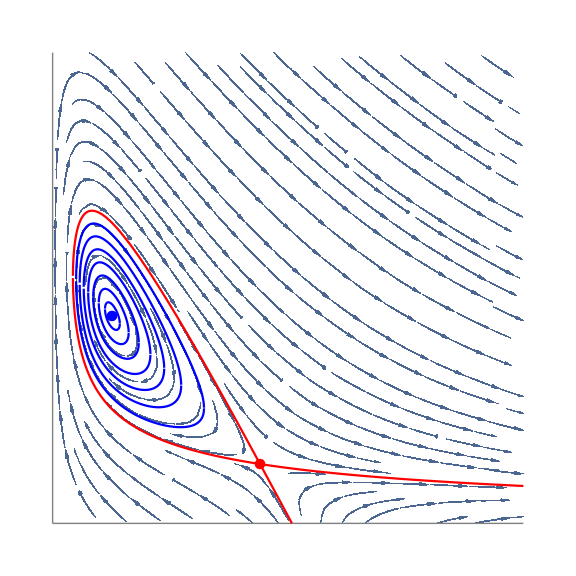

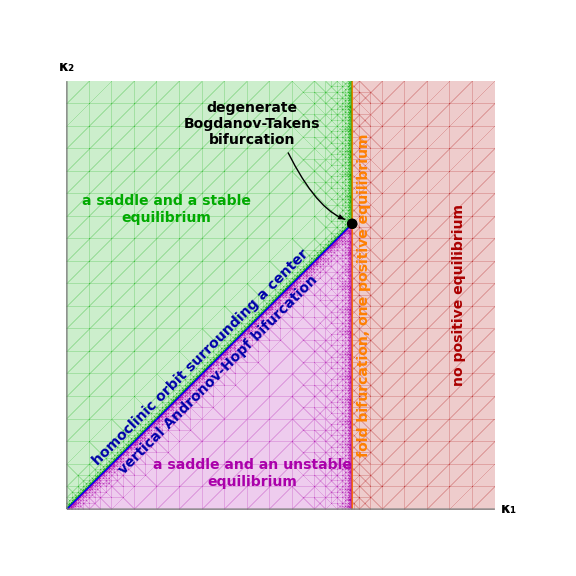

```mathematica
fg=GetRHS[ntws8[[9]]];
κsubst={Subscript[κ, 1]->2,Subscript[κ, 2]->2,Subscript[κ, 3]->1,Subscript[κ, 4]->3.4};
xylim=3;
H=Subscript[κ, 1] x y+Subscript[κ, 2]/2 y^2-Subscript[κ, 3] Log[x]-Subscript[κ, 4] y;
BogdanovTakensVerticalStreamPlot[fg,κsubst,xylim,H]
BogdanovTakensVerticalBifDiagr[]
```

#### Remark 34 (a)

We find that the 33 networks that admit a Bogdanov-Takens bifurcation fall into 28 diagonally nonequivalent classes.

```mathematica
FindDiagEquivAll[ntws8,"detailed"];
```

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        0 ⟶ Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        0 ⟶ Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0        X ⟶ Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0        X ⟶ 2Y

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ Y        X ⟶ 0

2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ Y        X ⟶ 0

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ X+2Y     X ⟶ 0

2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ X+Y      X ⟶ 0

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2X       0 ⟶ X+Y      X ⟶ 0

2X ⟶ 3X     X+Y ⟶ 3X       0 ⟶ 2X+Y     X ⟶ 0

-------------------------------------------------------

sources: {{0,0},{0,1},{1,1},{2,0}}; the   2 dynamically nonequivalent networks fall into   1 diagonally nonequivalent classes

sources: {{0,1},{1,0},{1,1},{2,0}}; the  17 dynamically nonequivalent networks fall into  16 diagonally nonequivalent classes

sources: {{0,0},{1,0},{1,1},{2,0}}; the   8 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,2},{1,0},{1,1},{2,0}}; the   5 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

sources: {{0,0},{0,2},{1,1},{2,0}}; the   1 dynamically nonequivalent networks fall into   1 diagonally nonequivalent classes

overall, the  33 dynamically nonequivalent networks fall into  28 diagonally nonequivalent classes

#### Remark 34 (b)

The Bogdanov-Takens bifurcation is supercritical in the network by Frank-Kamenetsky and Salnikov.

```mathematica
FrankKamenetskySalnikov["Bogdanov-Takens"];
```

(BT.0) Jordan normal form of the Jacobian matrix: (0 | 1
0 | 0)

(BT.1) and (BT.2)  equals -(y κ_2^5 (κ_2+κ_4))/(κ_4 (κ_2^2+κ_4^2))

(BT.3) transversality holds: True

#### Remark 34 (e)

The single network that admits a Bautin bifurcation also admits a Bogdanov-Takens bifurcation. However, the two codimension-two bifurcations occur in separate parts of the parameter space. As we have seen in Remark 31 (c) above, the Bautin bifurcation occurs at , while the double zero eigenvalue (and hence, the Bogdanov-Takens bifurcation) is at  (i.e., where  becomes zero).

#### Remark 34 (f)

The 7 networks that admit both a fold and an Andronov-Hopf bifurcation, but not a Bogdanov-Takens bifurcation.

```mathematica
ntws9=Complement[ntws6,ntws7][[{1,3,2,4,5,7,6}]];
PrintNtws[ntws9];
```

(1)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X

(2)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 3X

(3)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X+Y

(4)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ X

(5)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X

(6)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 3X

(7)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X+Y

The 7 networks fall into 5 diagonally nonequivalent classes.

```mathematica
FindDiagEquivAll[ntws9,"detailed"]
```

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ X

-------------------------------------------------------

2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 2X+Y

2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 2X

-------------------------------------------------------

sources: {{0,1},{0,2},{1,1},{2,0}}; the   7 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

overall, the   7 dynamically nonequivalent networks fall into   5 diagonally nonequivalent classes

## Appendix: Vertical Andronov-Hopf bifurcation

#### Lemma 39

We compute the condition on the rate constants under which  and  in the 20 networks that admit a vertical Andronov-Hopf bifurcation.

```mathematica
ntws=ntwsVerticalAH[[Join[Range[1,11],{14,15,12,13},Range[16,20]]]];
AndronovHopfVertical[ntws];
```

(1)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ Y        X ⟶ 2X    κ_1==κ_2+2 κ_3&&κ_2<κ_3

(2)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2Y       X ⟶ 2X    κ_1==κ_2+2 κ_3&&κ_2<2 κ_3

(3)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 3Y       X ⟶ 2X    κ_1==κ_2+2 κ_3&&κ_2<3 κ_3

(4)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ X+2Y     X ⟶ 2X    κ_1==κ_2+κ_3&&κ_2<2 κ_3

(5)  2X ⟶ 3X     X+Y ⟶ 0       2X ⟶ 2X+Y     X ⟶ 2X    κ_1==κ_2&&κ_2<κ_3

(6)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 0     κ_2 κ_3==κ_1 (κ_3+κ_4)

(7)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ X     κ_2 κ_3 (κ_3+κ_4)==κ_1 κ_4 (3 κ_3+κ_4)&&κ_3==κ_4

(8)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 2X    κ_2 κ_3 (2 κ_3+κ_4)==κ_1 κ_4 (5 κ_3+κ_4)&&κ_3==κ_4

(9)  2X ⟶ 3X     X+Y ⟶ Y        X ⟶ 2X+Y     Y ⟶ 3X    κ_2 κ_3 (3 κ_3+κ_4)==κ_1 κ_4 (7 κ_3+κ_4)&&κ_3==κ_4

(10)  2X ⟶ 3X     X+Y ⟶ 2Y       Y ⟶ 0       2Y ⟶ 0     κ_2==2 κ_4&&κ_1<2 κ_4

(11)  2X ⟶ 3X     X+Y ⟶ 3Y       Y ⟶ 0       2Y ⟶ 0     κ_2==2 κ_4&&κ_1<4 κ_4

(12)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        X ⟶ 2X    κ_1==κ_2&&κ_2>2 κ_3

(13)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        X ⟶ 2X    κ_1==2 κ_2&&κ_2>2 κ_3

(14)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        0 ⟶ X     κ_3==κ_2^2/(4 κ_1-2 κ_2)&&κ_1>κ_2

(15)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        0 ⟶ X     2 κ_3==κ_2^2/(κ_1-κ_2)&&κ_1>2 κ_2

(16)  2X ⟶ 3X     X+Y ⟶ 2Y      2Y ⟶ 0        Y ⟶ X+Y   4 κ_1 κ_3==κ_2 (κ_2+2 κ_3)&&κ_2>2 κ_3

(17)  2X ⟶ 3X     X+Y ⟶ 3Y      2Y ⟶ 0        Y ⟶ X+Y   2 (κ_1-κ_2) κ_3==κ_2^2&&κ_2>2 κ_3

(18)  2X ⟶ 3X     X+Y ⟶ X        X ⟶ 0        Y ⟶ X+2Y  κ_2 κ_3==2 κ_1 κ_4

(19)  2X ⟶ 3X     X+Y ⟶ 2X       X ⟶ 0        0 ⟶ Y     κ_1==κ_2&&κ_3^2>4 κ_2 κ_4

(20)  2X ⟶ 3X     X+Y ⟶ 3X       X ⟶ 0        0 ⟶ Y     κ_1==κ_2&&κ_3^2>8 κ_2 κ_4